```mathematica
Needs["Constants`"]
Needs["Capture`"]
Needs["Utilities`"]
Needs["EnergyLoss`"]
Needs["Dielectrics`"]
Needs["FormFactors`"]
```

## Early Unit Testing

#### bounds on 0 temp integral

```mathematica
qp = q/.Solve[q v +(ℏ q^2)/(2 mχ)== ω,q][[2,1]]
```

(-mχ v+√mχ √(mχ v^2+2 ω ℏ))/ℏ

```mathematica
qm = q/.Solve[q v -(ℏ q^2)/(2 mχ)== ω,q]
Solve[qm[[1]]==qm[[2]],ω]
```

{-(mχ (-v+(√(mχ v^2-2 ω ℏ))/(√mχ)))/ℏ,(mχ v+√mχ √(mχ v^2-2 ω ℏ))/ℏ}

{{ω→(mχ v^2)/(2 ℏ)}}

qm is lower bound, so we take

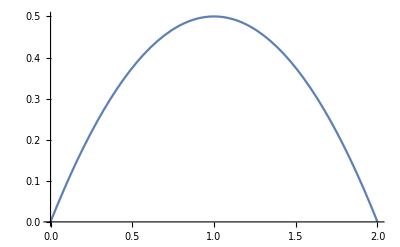

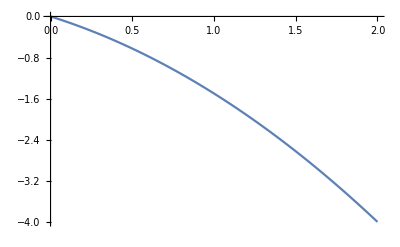

```mathematica
Plot[q-q^2/2,{q,0,2}]
Plot[-( q+q^2/2),{q,0,2}]
```

```mathematica
Solve[(ℏ^2 q^2)/(2 mN)==ℏ ω,q][[2]]
Solve[(ℏ^2 qm^2)/(2 mN)==ℏ ω,ω]
```

{{q→-(√2 √mN √ω)/(√ℏ)},{q→(√2 √mN √ω)/(√ℏ)}}

{}

```mathematica
Integrate[DiracDelta[(ℏ^2 q^2)/(2 mN)-ℏ ω],{q,qm[[1]],qm[[2]]}]
```

ConditionalExpression[Boole[(mχ v-√(mχ (mχ v^2-2 ω ℏ)))/ℏ<-√2 √((mN ω)/ℏ)<(mχ v+√(mχ (mχ v^2-2 ω ℏ)))/ℏ||(mχ v+√(mχ (mχ v^2-2 ω ℏ)))/ℏ<-√2 √((mN ω)/ℏ)<(mχ v-√(mχ (mχ v^2-2 ω ℏ)))/ℏ]/(√2 Abs[(ω ℏ)/(√((mN ω)/ℏ))]), ]

#### test dPdω - Nuclear

Kinetic over ℏ is (should bound ω)

```mathematica
1/(2 "ℏ")(2.5 10^7 ("JpereV")/("c")^2) (2.5 10^-5 "c")^2/.SIConstRepl
```

1.18632×10^13

```mathematica
Integrate[DiracDelta[(ℏ^2 q^2)/(2 mN)-ℏ ω],{q,√((2 mN ω)/ℏ)-ϵ,√((2 mN ω)/ℏ)+ϵ}]
```

ConditionalExpression[Boole[2 √2 √((mN ω)/ℏ)<ϵ||ϵ+2 √2 √((mN ω)/ℏ)<0]/(√2 Abs[(ω ℏ)/(√((mN ω)/ℏ))]), ]

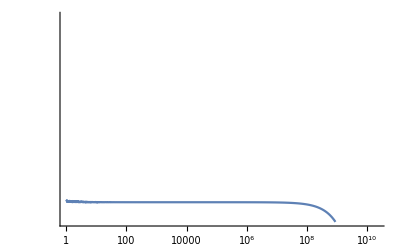

```mathematica
LogLogPlot[dPdωNuc0[ω,2.5 10^7 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-5 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl,<|"nI"->nIFe|>],{ω,10^0,10^15},PlotRange->{0,2.5 10^8}]
```

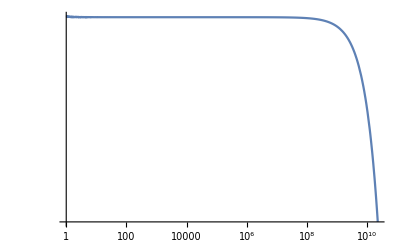

```mathematica
LogLogPlot[("JpereV"/.SIConstRepl)dσdERNuc0[ω,2.5 10^7 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-5 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl],{ω,10^0,10^15},PlotRange->All]
```

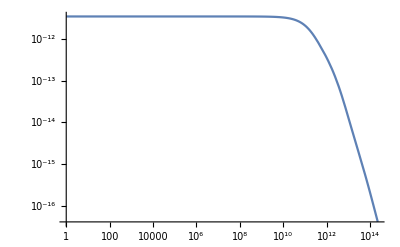

```mathematica
LogLogPlot[("JpereV"/.SIConstRepl)dσdERNuc0[ω,2.5 10^8 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-4 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl],{ω,10^0,10^15},PlotRange->All]
```

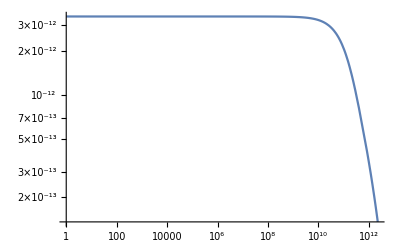

```mathematica
LogLogPlot[("JpereV"/.SIConstRepl)dσdERNuc0[ω,2.5 10^7 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-4 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl],{ω,10^0,10^15},PlotRange->All]
```

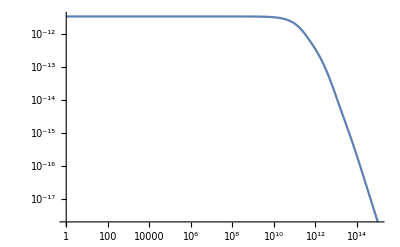

```mathematica
LogLogPlot[("JpereV"/.SIConstRepl)dσdERNuc0[ω,2.5 10^10 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-4 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl],{ω,10^0,10^15},PlotRange->All]
```

General::munfl: Exp[-10180.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2033.03] is too small to represent as a normalized machine number; precision may be lost.

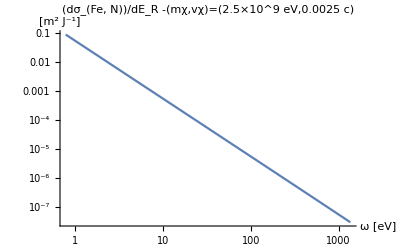

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^9 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;LogLogPlot[dσdERNuc0[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeNucCoeffs,SIConstRepl],{ω,10^-4 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotRange->All,PlotLabel->StringForm["(dσ_(Fe, N))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

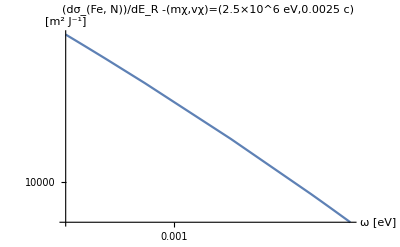

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;LogLogPlot[dσdERNuc0[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeNucCoeffs,SIConstRepl],{ω,10^-4 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotRange->All,PlotLabel->StringForm["(dσ_(Fe, N))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

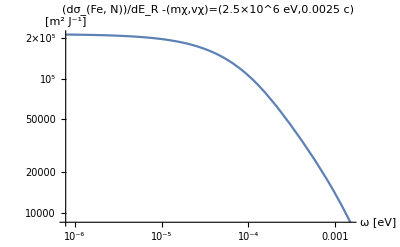

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;LogLogPlot[dσdERNuc0[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeNucCoeffs,SIConstRepl],{ω,10^-7 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,1.1ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotRange->All,PlotLabel->StringForm["(dσ_(Fe, N))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

#### Check f(ω) enhancement

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

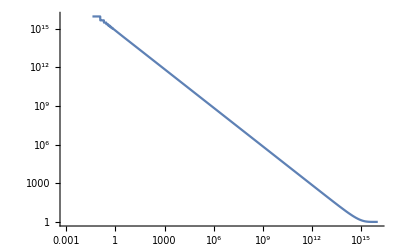

```mathematica
LogLogPlot[1/(1 - E^(-"β" "ℏ" ω))/.SIConstRepl/."β"->βcore,{ω,10^-3,10^16}]
```

```mathematica
"β"/.SIConstRepl/."β"->βcore
```

1.32379×10^19

I think it should be that this enhancement only becomes large for ℏ ω <~ 0.024 eV

```mathematica
1/("β""JpereV")/.SIConstRepl/."β"->βcrust
```

0.0249994

```mathematica
("ℏ")/("JpereV")/.SIConstRepl/."β"->βcrust
```

6.58552×10^-16

yes that’s true, this is an eV in s^{-1}, which means the point where our plot above becomes large still corresponds to temperature larger than the energy transfer (which is sub eV scale)

**** May need to rerun things. at MeV dm mass and 10^-3 c this will be upper bound on DM. So some of our EL plots are not valid.

#### test dPdω - Electronic

```mathematica
dPdωe[10^16,2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-3 "c"/.SIConstRepl,FeTotalparams,βcore]
```

0.0834743

```mathematica
zIntegraldσdER[10^16,2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-3 "c"/.SIConstRepl,FeTotalparams]
```

0.089818

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Plot[dσdERe[ω,mχtemp,vχtemp,FeTotalparams],{ω,10^-2 ERmaxtemp,ERmaxtemp}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000090050838026805373154153044890080082041095010936260223388671875}. NIntegrate obtained 1.66857×10^-10 and 2.19482×10^-15 for the integral and error estimates.

-Graphics-

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Plot[dσdERe[ω,mχtemp,vχtemp,FeTotalparams],{ω,-10^-2 ERmaxtemp,-ERmaxtemp}]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000738861}. NIntegrate obtained -0.139433 and 0.143475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000602395}. NIntegrate obtained -0.0769584 and 0.190817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000458506}. NIntegrate obtained -0.171785 and 0.272143 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000090050838026805373154153044890080082041095010936260223388671875}. NIntegrate obtained 1.66857×10^-10 and 2.19482×10^-15 for the integral and error estimates.

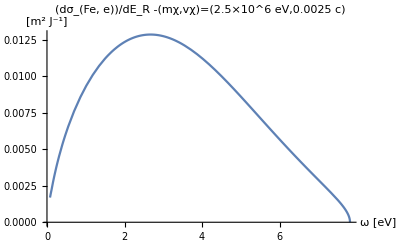

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeTotalparams],{ω,10^-2 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,vχtemp("c")^-1/.SIConstRepl],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000090050838026805373154153044890080082041095010936260223388671875}. NIntegrate obtained 1.66857×10^-10 and 2.19482×10^-15 for the integral and error estimates.

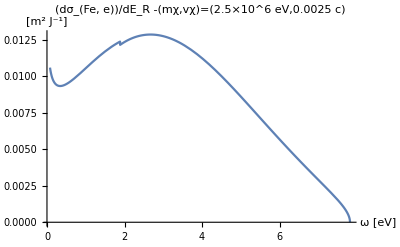

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeTotalparams,βcore],{ω,10^-2 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

## Interpolation and Plots

### Electronic - Unit Testing

#### Initialize

```mathematica
Clear[FeλeDictOscillators,MgOλeDictOscillators,SiO2λeDictOscillators]
FeλeDictOscillators=Table[ReadIt[NotebookDirectory[]<>ToString[StringForm["../capture/FeλeDictSIOscillator_``",i]]],{i,6}];
MgOλeDictOscillators=Table[ReadIt[NotebookDirectory[]<>ToString[StringForm["../capture/MgOλeDictSIOscillator_``",i]]],{i,4}];
SiO2λeDictOscillators=Table[ReadIt[NotebookDirectory[]<>ToString[StringForm["../capture/SiO2λeDictSIOscillator_``",i]]],{i,2}];
```

```mathematica
MgOλeDictOscillators
```

{<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{354.918,768.812,5409.72,1.21586×10^6},{14902.,28251.6,3.1106×10^6,2.06956×10^6},{341994.,1.24053×10^7,8.90137×10^7,2.08423×10^6},{4.53128×10^7,1.55788×10^8,9.14485×10^7,2.08404×10^6},{1.65742×10^8,1.73392×10^8,9.15018×10^7,2.08385×10^6},{1.75003×10^8,1.74271×10^8,9.08275×10^7,2.08895×10^6},{1.74964×10^8,1.73886×10^8,9.1821×10^7,2.37771×10^6},{1.74628×10^8,1.75572×10^8,9.09635×10^7,2.085×10^6}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0}},fname→MgOλeDictSIOscillator_1,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{559.696,286.53,145.795,18.4415},{193.755,118.039,12.6621,48.3262},{1.16981,15.4046,41.8852,49.6891},{11.3519,12.1511,48.9862,86.3756},{25.6958,54.9955,295.594,170.166},{102.394,159.317,251.398,180.919},{177.922,184.392,129.044,168.91},{109.622,85.9449,86.5212,73.8572}},totalTime→3906.95|>,<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{796.014,1739.83,12249.1,6.67418×10^6},{33453.1,64153.8,6.63895×10^6,1.36713×10^7},{780192.,3.23747×10^7,5.18417×10^8,1.37213×10^7},{1.29219×10^8,6.41442×10^8,5.46568×10^8,1.38655×10^7},{6.92111×10^8,7.35822×10^8,5.47729×10^8,1.41957×10^7},{7.42254×10^8,7.40812×10^8,5.48738×10^8,1.32216×10^7},{7.51635×10^8,7.40432×10^8,7.0302×10^8,1.29006×10^7},{7.44104×10^8,7.52668×10^8,5.49303×10^8,1.37956×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0}},fname→MgOλeDictSIOscillator_2,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{697.048,207.605,151.603,13.9312},{212.217,116.486,10.1696,37.9802},{0.0817729,5.1727,24.0577,63.0149},{6.2106,13.0841,33.0516,84.4595},{44.1347,47.3527,124.752,206.968},{69.2424,120.22,238.966,317.834},{160.629,152.342,483.978,154.276},{98.4904,90.3671,73.8148,62.0724}},totalTime→4121.61|>,<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{355.864,778.261,5541.61,3.67155×10^6},{15071.4,29024.1,3.03746×10^6,7.9761×10^6},{353799.,1.52239×10^7,2.90996×10^8,8.05428×10^6},{6.20112×10^7,3.35101×10^8,3.09889×10^8,8.15849×10^6},{3.6295×10^8,3.87522×10^8,3.10594×10^8,8.2506×10^6},{3.90654×10^8,3.90437×10^8,2.74101×10^8,4.72241×10^-11},{3.87865×10^8,3.90363×10^8,3.47174×10^8,8.14859×10^6},{3.91792×10^8,3.92519×10^8,3.08731×10^8,8.09132×10^6}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0}},fname→MgOλeDictSIOscillator_3,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{351.975,226.397,107.258,10.4982},{202.247,113.335,10.7812,38.1239},{0.0824922,5.66131,35.9782,62.0736},{6.96256,12.2447,32.0465,80.657},{17.7364,46.6912,124.197,207.882},{69.6034,118.815,322.366,64.7216},{164.643,166.975,305.231,108.632},{108.179,81.7594,76.2935,59.8034}},totalTime→3339.85|>,<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{0.942814,11607.3,138698.,1.03641×10^7},{287000.,717421.,4.88354×10^7,4.48922×10^7},{8.51375×10^6,1.68522×10^8,1.31388×10^9,4.64975×10^7},{5.21508×10^8,2.53959×10^9,1.53794×10^9,4.65158×10^7},{2.82624×10^9,3.00904×10^9,1.54895×10^9,4.64478×10^7},{3.08357×10^9,3.03421×10^9,1.54954×10^9,4.12294×10^7},{3.09734×10^9,3.02784×10^9,1.53294×10^9,4.65524×10^7},{3.10039×10^9,3.00549×10^9,1.5798×10^9,4.65198×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0}},fname→MgOλeDictSIOscillator_4,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{800.964,430.794,228.308,120.685},{295.382,207.197,95.7963,55.9759},{217.961,32.9945,8.58606,67.5093},{95.9224,48.2882,28.3616,43.5753},{78.8993,31.7338,83.1852,301.87},{102.971,139.423,221.146,567.59},{159.35,169.08,396.26,144.255},{183.046,109.511,151.093,75.5189}},totalTime→5693.23|>}

#### Computed Cross-Sections

```mathematica
(*Clear[FenesOscillator,FeσsOscillator]
FenesOscillator= Table[("ne"/.FeλeDictOscillators[[i]][["fitparams"]][[1]]),{i,Length[FeλeDictOscillators]}]
FeσsOscillator=Table[(10^(FeλeDictOscillators[[i]][["f"]][#1,#2])/FenesOscillator[[i]]),{i,Length[FeλeDictOscillators]}]*)
```

```mathematica
Show[Table[LogLogPlot[(FeλeDictOscillators[[i]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[i]][["fitparams"]][[1]]),{mχ,2"m"/.SIConstRepl,2 10^5"m"/.SIConstRepl},PlotRange->{10^-42,10^-27},PlotLabels->ToString[StringForm["``",i]],PlotLabel->"Fe σ Per Oscillator - vχ = 10^-3 c",AxesLabel->{"mχ [kg]","[m^2]"}],{i,Length[FeλeDictOscillators]}]]
Print["From this plot we see that as expected, the outer electron shells dominate the cross-section for Iron"]
```

-Graphics-

From this plot we see that as expected, the outer electron shells dominate the cross-section for Iron

Show the same plots as above, but with only one oscillator each to show the profile

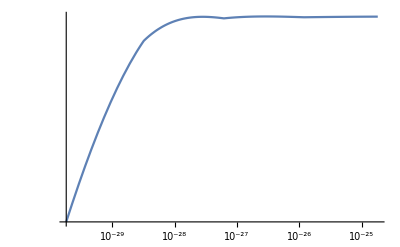

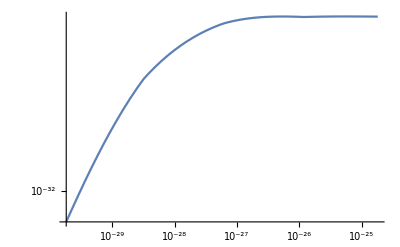

```mathematica
Print["Show the same plots as above, but with only one oscillator each to show the profile"]
LogLogPlot[(FeλeDictOscillators[[1]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[1]][["fitparams"]][[1]]),{mχ,2"m"/.SIConstRepl,2 10^5"m"/.SIConstRepl}]
LogLogPlot[(FeλeDictOscillators[[5]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[5]][["fitparams"]][[1]]),{mχ,2"m"/.SIConstRepl,2 10^5"m"/.SIConstRepl}]
```

```mathematica
Print["Extend the range of masses"]
Show[Table[LogLogPlot[(FeλeDictOscillators[[i]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[i]][["fitparams"]][[1]]),{mχ,10^-32.3, 10^-23.4},PlotRange->{10^-42,10^-27},PlotLabels->ToString[StringForm["``",i]],PlotLabel->"Fe σ Per Oscillator - vχ = 10^-3 c",AxesLabel->{"mχ [kg]","[m^2]"}],{i,Length[FeλeDictOscillators]}]]
Print["Why are some of the oscillators being truncated at the same value of the mass? I would have guessed it would be the energy truncation we did, but because oscillator 4 is untruncated, this seems unlikely. So lets look at the values ω_(edge, i) where they were truncated at"]
"ωedgei"/.Table[FeλeDictOscillators[[i]][["fitparams"]][[1]],{i,Length[FeλeDictOscillators]}]
Print["And also the number densities"]
"ne"/.Table[FeλeDictOscillators[[i]][["fitparams"]][[1]],{i,Length[FeλeDictOscillators]}]
```

Extend the range of masses

-Graphics-

Why are some of the oscillators being truncated at the same value of the mass? I would have guessed it would be the energy truncation we did, but because oscillator 4 is untruncated, this seems unlikely. So lets look at the values ω_(edge, i) where they were truncated at

{6.04519×10^14,6.5887×10^12,3.02977×10^14,1.51848×10^14,1.09042×10^18,1.09893×10^19}

And also the number densities

{1.038×10^29,1.91532×10^29,4.34359×10^29,3.17873×10^30,4.14995×10^32,4.0004×10^34}

```mathematica
LogLogPlot[(FeλeDictOscillators[[3]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[3]][["fitparams"]][[1]]),{mχ,10^-32.3, 10^-23.4},PlotLabels->ToString[StringForm["``",3]],PlotLabel->"Fe σ Per Oscillator - vχ = 10^-3 c",AxesLabel->{"mχ [kg]","[m^2]"}]
```

-Graphics-

#### Recoil Energy Sampling

```mathematica
FeλeDictOscillators[[1]][["fitparams"]][[1]]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14}

```mathematica
EarthRepl
```

<|rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→290,Tcore→5470,βcrust→2.49694×10^20,βcore→1.32379×10^19,SiO2Frac→0.447,MgOFrac→0.387|>

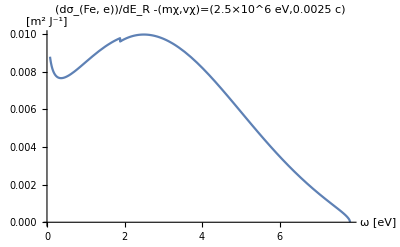

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[1]][["fitparams"]],βcore],{ω,10^-2 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

Now include the truncation due to the cutoff of available data

1.18632×10^16

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000310856}. NIntegrate obtained 0.0000421186 and 6.94605×10^-7 for the integral and error estimates.

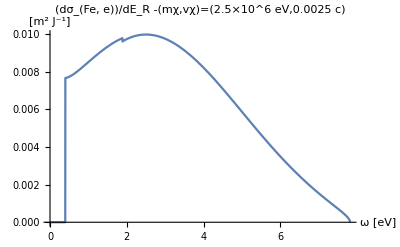

Notice that this is a cutoff sub eV

```mathematica
Print["Now include the truncation due to the cutoff of available data"]
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ERmaxtemp];
Print[Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[1]][["fitparams"]],βcore]HeavisideTheta[(("JpereV")/("ℏ"))ω-"ωedgei"/.FeλeDictOscillators[[1]][["fitparams"]][[1]]],{ω,0ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]]
]
Print["Notice that this is a cutoff sub eV"]
```

Lets look at the outermost shell

1.18632×10^16

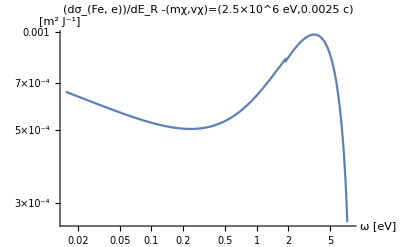

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00010936}. NIntegrate obtained 4.91141×10^-6 and 1.73417×10^-7 for the integral and error estimates.

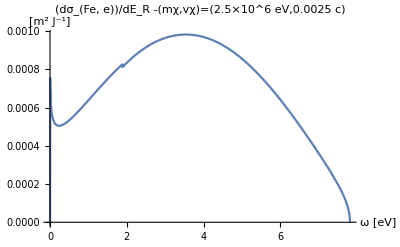

Notice this has a much lower cutoff

```mathematica
Print["Lets look at the outermost shell"]
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ERmaxtemp];
Print[LogLogPlot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[2]][["fitparams"]],βcore]HeavisideTheta[(("JpereV")/("ℏ"))ω-"ωedgei"/.FeλeDictOscillators[[2]][["fitparams"]][[1]]],{ω,0ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]];
Print[Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[2]][["fitparams"]],βcore]HeavisideTheta[(("JpereV")/("ℏ"))ω-"ωedgei"/.FeλeDictOscillators[[2]][["fitparams"]][[1]]],{ω,0ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]]
]
Print["Notice this has a much lower cutoff"]
```

```mathematica
Testdσfunc[["dσTable"]][[;;,1]](("JpereV")/("ℏ"))^-1/.SIConstRepl
```

{0.004339,0.00620024,0.00885988,0.0126604,0.0180911,0.0258515,0.0369406,0.0527865,0.0754297,0.107786,0.154021,0.22009,0.314498,0.449405,0.64218,0.917647,1.31128,1.87376,2.67752,3.82606}

To interpolate, we need to determine the range over which to interpolate, and then evaluate the function at the points in a list, then interpolate

For the range: we want to evaluate from ω_(edge,i), then have some set number of evaluations, then we can do the interpolation

we also want to do this for each oscillator.

```mathematica
Testdσfunc=Block[{mχ,vχ,params,ERmin,ERmax,InterPω,n=20,InterdσTable,Interdσf},
(*Input parameters*)
mχ = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχ = 2.5 10^-3 "c"/.SIConstRepl;
params = FeλeDictOscillators[[2]][["fitparams"]][[1]];

(*local parameters*)
ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];

Print[dσdERe[ERmax,mχ,vχ,{params},"β"/.params]];
Print[ERmax];
Print[InterPω[[n+1]]];
Print[ERmax==InterPω[[n+1]]];
Print[dσdERe[N[InterPω[[n+1]](1-10^-3)],mχ,vχ,{params},"β"/.params]];

InterdσTable=Table[{InterPω[[i]],dσdERe[InterPω[[i]](1-10^-3),mχ,vχ,{params},"β"/.params]HeavisideTheta[InterPω[[i]]-ERmin]},{i,n+1}];
Interdσf=Interpolation[InterdσTable];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->InterPω|>
]
```

0.

1.18632×10^16

1.18632×10^16

True

0.0000287166

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0003463745696036182202849629252483509844751097261905670166015625}. NIntegrate obtained 0.000113854 and 6.1034×10^-9 for the integral and error estimates.

<|dσf→InterpolatingFunction[…],dσTable→{{6.5887×10^12,0.000763026},{9.58451×10^12,0.000730472},{1.39425×10^13,0.000698427},{2.0282×10^13,0.000667086},{2.95039×10^13,0.000636717},{4.2919×10^13,0.000607674},{6.24338×10^13,0.000580439},{9.08217×10^13,0.00055567},{1.32117×10^14,0.000534269},{1.9219×10^14,0.000517488},{2.79576×10^14,0.000507088},{4.06696×10^14,0.000505583},{5.91616×10^14,0.000516596},{8.60617×10^14,0.000545281},{1.25193×10^15,0.000598449},{1.82117×10^15,0.000683001},{2.64923×10^15,0.00079926},{3.85381×10^15,0.000919998},{5.60609×10^15,0.000980598},{8.15511×10^15,0.000787263},{1.18632×10^16,0.0000287166}},Interpoints→{6.5887×10^12,9.58451×10^12,1.39425×10^13,2.0282×10^13,2.95039×10^13,4.2919×10^13,6.24338×10^13,9.08217×10^13,1.32117×10^14,1.9219×10^14,2.79576×10^14,4.06696×10^14,5.91616×10^14,8.60617×10^14,1.25193×10^15,1.82117×10^15,2.64923×10^15,3.85381×10^15,5.60609×10^15,8.15511×10^15,1.18632×10^16}|>

```mathematica
(*InterpolatedσdERe[mχ_,vχ_,params_]:=Module[{ERmin,ERmax,InterPω,ϵ,n=20,InterdσTable,Interdσf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)
(*local parameters*)
ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];
ϵ=10^-10;(*Subdivide takes us slightly over ERmax, which throws errors. So subtract off a small fraction ϵ of ER max*)

InterdσTable=Table[{InterPω[[i]],dσdERe[InterPω[[i]](1-ϵ),mχ,vχ,{params},"β"/.params]HeavisideTheta[InterPω[[i]]-ERmin]},{i,n+1}];
Interdσf=Interpolation[InterdσTable];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->InterPω|>
]*)
```

```mathematica
InterpolatedσdERe2 =InterpolatedσdERe[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-3 "c"/.SIConstRepl, FeλeDictOscillators[[2]][["fitparams"]][[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0002782473013753506880271597345721801275431062094867229461669921875}. NIntegrate obtained 0.000113954 and 6.13129×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000602666718839405825790256354679286232567392289638519287109375}. NIntegrate obtained 0.000158367 and 1.4707×10^-9 for the integral and error estimates.

<|dσf→InterpolatingFunction[…],dσTable→{{6.5887×10^12,0.000762938},{9.58451×10^12,0.000730402},{1.39425×10^13,0.000698342},{2.0282×10^13,0.000667004},{2.95039×10^13,0.000636637},{4.2919×10^13,0.000607598},{6.24338×10^13,0.000580369},{9.08217×10^13,0.000555607},{1.32117×10^14,0.000534217},{1.9219×10^14,0.000517451},{2.79576×10^14,0.000507071},{4.06696×10^14,0.000505594},{5.91616×10^14,0.000516646},{8.60617×10^14,0.000545387},{1.25193×10^15,0.00059863},{1.82117×10^15,0.000683272},{2.64923×10^15,0.000799601},{3.85381×10^15,0.000920314},{5.60609×10^15,0.000980529},{8.15511×10^15,0.000786165},{1.18632×10^16,9.05968×10^-9}},Interpoints→{6.5887×10^12,9.58451×10^12,1.39425×10^13,2.0282×10^13,2.95039×10^13,4.2919×10^13,6.24338×10^13,9.08217×10^13,1.32117×10^14,1.9219×10^14,2.79576×10^14,4.06696×10^14,5.91616×10^14,8.60617×10^14,1.25193×10^15,1.82117×10^15,2.64923×10^15,3.85381×10^15,5.60609×10^15,8.15511×10^15,1.18632×10^16}|>

```mathematica
Print["Show the Block which we've tested, and the module we have written give the same expression"]
Plot[Testdσfunc[["dσf"]][ω],{ω,Testdσfunc[["Interpoints"]][[1]],Testdσfunc[["Interpoints"]][[-1]]}]
Plot[InterpolatedσdERe2 [["dσf"]][ω],{ω,InterpolatedσdERe2 [["Interpoints"]][[1]],InterpolatedσdERe2 [["Interpoints"]][[-1]]}]
```

Show the Block which we've tested, and the module we have written give the same expression

-Graphics-

-Graphics-

```mathematica
NIntegrate[Testdσfunc[["dσf"]][ω],{ω,Testdσfunc[["Interpoints"]][[1]],Testdσfunc[["Interpoints"]][[-1]]}]
```

8.37856×10^12

#### Interpolate over vχ as well as ω - Doesn’t Work

```mathematica
GetvχandωList[mχ_,vχ_,params_,n_:20]:=Module[{ERmin,ERmax,ϵ,Interpointsω},
ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;

Interpointsω=10^Subdivide[Log10[ERmin],Log10[ERmax],n];
Table[{vχ,Interpointsω[[i]]},{i,n+1}]
]
```

```mathematica
GetvχandωList[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-3 "c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]]]
```

{{750000.,6.5887×10^12},{750000.,9.58451×10^12},{750000.,1.39425×10^13},{750000.,2.0282×10^13},{750000.,2.95039×10^13},{750000.,4.2919×10^13},{750000.,6.24338×10^13},{750000.,9.08217×10^13},{750000.,1.32117×10^14},{750000.,1.9219×10^14},{750000.,2.79576×10^14},{750000.,4.06696×10^14},{750000.,5.91616×10^14},{750000.,8.60617×10^14},{750000.,1.25193×10^15},{750000.,1.82117×10^15},{750000.,2.64923×10^15},{750000.,3.85381×10^15},{750000.,5.60609×10^15},{750000.,8.15511×10^15}}

```mathematica
InterpolatvχandωσdERe[mχ_,vχ_:{10^-5,10^-2}"c"/.SIConstRepl,params_,m_:4,n_:20]:=Module[{ωmin,Interpointsvχ,Interpointsvχandω,ϵ,InterdσTable,Interdσf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

(*local parameters*)
(*ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];*)
ωmin= "ωedgei"/.params;
Interpointsvχ=10^Subdivide[Log10[vχ[[1]]],Log10[vχ[[2]]],m];
Interpointsvχandω=SortBy[Table[GetvχandωList[mχ,Interpointsvχ[[i]],params,n],{i,m+1}],Last];
ϵ=10^-4;(*Subdivide takes us slightly over ERmax, which throws errors. So subtract off a small fraction ϵ of ER max*)
(*Print[Interpointsvχandω[[1,1]][[1]]];
Print[Interpointsvχandω[[1,1]][[2]]];*)
(*Print[dσdERe[6.588699526066354*^12(1+ϵ),mχ,3000(1+ϵ),{params},"β"/.params]];
Print[dσdERe[Interpointsvχandω[[1,1]][[2]](1+ϵ),mχ,Interpointsvχandω[[1,1]][[1]],{params},"β"/.params]];*)
InterdσTable=Table[{Interpointsvχandω[[i,j]],dσdERe[Interpointsvχandω[[i,j]][[2]],mχ,Interpointsvχandω[[i,j]][[1]],{params},"β"/.params]HeavisideTheta[Interpointsvχandω[[i,j]][[2]]-ωmin]},{i,m+1},{j,n+1}];
Interdσf=Interpolation[Flatten[Log10[InterdσTable],1]];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->Interpointsvχandω,"Interpointsvχ"->Interpointsvχ|>
]
```

```mathematica
testkinσinterpolate=InterpolatvχandωσdERe[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{10^-4,10^-2}"c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]],4,20]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000125028}. NIntegrate obtained 0.000128098 and 1.87966×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00023053}. NIntegrate obtained 0.000210627 and 6.68139×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00019964873741304990040971827081062173192549380473792552947998046875}. NIntegrate obtained 0.000331927 and 4.00527×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

<|dσf→InterpolatingFunction[…],dσTable→{{{{30000,6.5887×10^12},0.128779},{{30000,6.94665×10^12},0.125043},{{30000,7.32406×10^12},0.121248},{{30000,7.72196×10^12},0.117387},{{30000,8.14149×10^12},0.113453},{{30000,8.5838×10^12},0.109437},{{30000,9.05015×10^12},0.10533},{{30000,9.54183×10^12},0.101119},{{30000,1.00602×10^13},0.0967902},{{30000,1.06068×10^13},0.0923255},{{30000,1.1183×10^13},0.0877034},{{30000,1.17906×10^13},0.0828965},{{30000,1.24312×10^13},0.0778694},{{30000,1.31065×10^13},0.0725748},{{30000,1.38186×10^13},0.066948},{{30000,1.45693×10^13},0.060895},{{30000,1.53609×10^13},0.0542717},{{30000,1.61954×10^13},0.0468342},{{30000,1.70753×10^13},0.0381056},{{30000,1.8003×10^13},0.0268509},{{30000,1.8981×10^13},1.16337×10^-6}},{{{300000,6.5887×10^12},0.00414931},{{300000,8.74532×10^12},0.00399408},{{300000,1.16078×10^13},0.00384017},{{300000,1.54073×10^13},0.00368792},{{300000,2.04505×10^13},0.00353772},{{300000,2.71444×10^13},0.00339007},{{300000,3.60293×10^13},0.00324558},{{300000,4.78225×10^13},0.00310498},{{300000,6.34758×10^13},0.00296914},{{300000,8.42527×10^13},0.00283909},{{300000,1.1183×10^14},0.00271602},{{300000,1.48435×10^14},0.00260126},{{300000,1.97021×10^14},0.00249623},{{300000,2.6151×10^14},0.00240224},{{300000,3.47107×10^14},0.00232005},{{300000,4.60723×10^14},0.00224882},{{300000,6.11528×10^14},0.00218355},{{300000,8.11693×10^14},0.00210868},{{300000,1.07738×10^15},0.00198043},{{300000,1.43003×10^15},0.00166523},{{300000,1.8981×10^15},3.83751×10^-8}},{{{3000000,6.5887×10^12},0.0000536022},{{3000000,1.10097×10^13},0.0000529074},{{3000000,1.83972×10^13},0.0000501535},{{3000000,3.07417×10^13},0.0000476051},{{3000000,5.13693×10^13},0.0000452776},{{3000000,8.5838×10^13},0.0000432816},{{3000000,1.43435×10^14},0.0000418077},{{3000000,2.3968×10^14},0.0000411727},{{3000000,4.00505×10^14},0.00004192},{{3000000,6.69243×10^14},0.0000450281},{{3000000,1.1183×10^15},0.0000523279},{{3000000,1.86868×10^15},0.0000672103},{{3000000,3.12257×10^15},0.0000942808},{{3000000,5.21781×10^15},0.0001489},{{3000000,8.71895×10^15},0.000289498},{{3000000,1.45693×10^16},0.000555831},{{3000000,2.43453×10^16},0.000104805},{{3000000,4.0681×10^16},0.0000262153},{{3000000,6.79779×10^16},8.02963×10^-6},{{3000000,1.13591×10^17},2.59059×10^-6},{{3000000,1.8981×10^17},2.65079×10^-14}},{{{30000 √10,6.5887×10^12},0.0279111},{{30000 √10,7.79427×10^12},0.0269579},{{30000 √10,9.22044×10^12},0.0260032},{{30000 √10,1.09076×10^13},0.0250463},{{30000 √10,1.29034×10^13},0.0240866},{{30000 √10,1.52644×10^13},0.0231232},{{30000 √10,1.80574×10^13},0.0221549},{{30000 √10,2.13615×10^13},0.0211802},{{30000 √10,2.52702×10^13},0.0201969},{{30000 √10,2.9894×10^13},0.0192024},{{30000 √10,3.53639×10^13},0.018193},{{30000 √10,4.18346×10^13},0.0171637},{{30000 √10,4.94894×10^13},0.0161076},{{30000 √10,5.85447×10^13},0.0150151},{{30000 √10,6.9257×10^13},0.0138721},{{30000 √10,8.19294×10^13},0.0126577},{{30000 √10,9.69206×10^13},0.0113384},{{30000 √10,1.14655×10^14},0.00985722},{{30000 √10,1.35634×10^14},0.00810197},{{30000 √10,1.60452×10^14},0.00578626},{{30000 √10,1.8981×10^14},1.43132×10^-7}},{{{300000 √10,6.5887×10^12},0.000490234},{{300000 √10,9.81241×10^12},0.000468611},{{300000 √10,1.46134×10^13},0.000447422},{{300000 √10,2.17635×10^13},0.000426766},{{300000 √10,3.24118×10^13},0.000406875},{{300000 √10,4.82703×10^13},0.00038805},{{300000 √10,7.18879×10^13},0.000370713},{{300000 √10,1.07061×10^14},0.00035546},{{300000 √10,1.59444×10^14},0.000343132},{{300000 √10,2.37456×10^14},0.000334941},{{300000 √10,3.53639×10^14},0.000332674},{{300000 √10,5.26667×10^14},0.000339008},{{300000 √10,7.84354×10^14},0.000358055},{{300000 √10,1.16812×10^15},0.000395656},{{300000 √10,1.73966×10^15},0.000459763},{{300000 √10,2.59084×10^15},0.000556967},{{300000 √10,3.85848×10^15},0.000680416},{{300000 √10,5.74635×10^15},0.00080825},{{300000 √10,8.55792×10^15},0.000829791},{{300000 √10,1.27451×10^16},0.000502176},{{300000 √10,1.8981×10^16},2.26382×10^-9}}},Interpoints→{{{30000,6.5887×10^12},{30000,6.94665×10^12},{30000,7.32406×10^12},{30000,7.72196×10^12},{30000,8.14149×10^12},{30000,8.5838×10^12},{30000,9.05015×10^12},{30000,9.54183×10^12},{30000,1.00602×10^13},{30000,1.06068×10^13},{30000,1.1183×10^13},{30000,1.17906×10^13},{30000,1.24312×10^13},{30000,1.31065×10^13},{30000,1.38186×10^13},{30000,1.45693×10^13},{30000,1.53609×10^13},{30000,1.61954×10^13},{30000,1.70753×10^13},{30000,1.8003×10^13},{30000,1.8981×10^13}},{{300000,6.5887×10^12},{300000,8.74532×10^12},{300000,1.16078×10^13},{300000,1.54073×10^13},{300000,2.04505×10^13},{300000,2.71444×10^13},{300000,3.60293×10^13},{300000,4.78225×10^13},{300000,6.34758×10^13},{300000,8.42527×10^13},{300000,1.1183×10^14},{300000,1.48435×10^14},{300000,1.97021×10^14},{300000,2.6151×10^14},{300000,3.47107×10^14},{300000,4.60723×10^14},{300000,6.11528×10^14},{300000,8.11693×10^14},{300000,1.07738×10^15},{300000,1.43003×10^15},{300000,1.8981×10^15}},{{3000000,6.5887×10^12},{3000000,1.10097×10^13},{3000000,1.83972×10^13},{3000000,3.07417×10^13},{3000000,5.13693×10^13},{3000000,8.5838×10^13},{3000000,1.43435×10^14},{3000000,2.3968×10^14},{3000000,4.00505×10^14},{3000000,6.69243×10^14},{3000000,1.1183×10^15},{3000000,1.86868×10^15},{3000000,3.12257×10^15},{3000000,5.21781×10^15},{3000000,8.71895×10^15},{3000000,1.45693×10^16},{3000000,2.43453×10^16},{3000000,4.0681×10^16},{3000000,6.79779×10^16},{3000000,1.13591×10^17},{3000000,1.8981×10^17}},{{30000 √10,6.5887×10^12},{30000 √10,7.79427×10^12},{30000 √10,9.22044×10^12},{30000 √10,1.09076×10^13},{30000 √10,1.29034×10^13},{30000 √10,1.52644×10^13},{30000 √10,1.80574×10^13},{30000 √10,2.13615×10^13},{30000 √10,2.52702×10^13},{30000 √10,2.9894×10^13},{30000 √10,3.53639×10^13},{30000 √10,4.18346×10^13},{30000 √10,4.94894×10^13},{30000 √10,5.85447×10^13},{30000 √10,6.9257×10^13},{30000 √10,8.19294×10^13},{30000 √10,9.69206×10^13},{30000 √10,1.14655×10^14},{30000 √10,1.35634×10^14},{30000 √10,1.60452×10^14},{30000 √10,1.8981×10^14}},{{300000 √10,6.5887×10^12},{300000 √10,9.81241×10^12},{300000 √10,1.46134×10^13},{300000 √10,2.17635×10^13},{300000 √10,3.24118×10^13},{300000 √10,4.82703×10^13},{300000 √10,7.18879×10^13},{300000 √10,1.07061×10^14},{300000 √10,1.59444×10^14},{300000 √10,2.37456×10^14},{300000 √10,3.53639×10^14},{300000 √10,5.26667×10^14},{300000 √10,7.84354×10^14},{300000 √10,1.16812×10^15},{300000 √10,1.73966×10^15},{300000 √10,2.59084×10^15},{300000 √10,3.85848×10^15},{300000 √10,5.74635×10^15},{300000 √10,8.55792×10^15},{300000 √10,1.27451×10^16},{300000 √10,1.8981×10^16}}},Interpointsvχ→{30000,30000 √10,300000,300000 √10,3000000}|>

```mathematica
testkinσinterpolate[["dσf"]][5,13]
```

Missing[KeyAbsent,5]

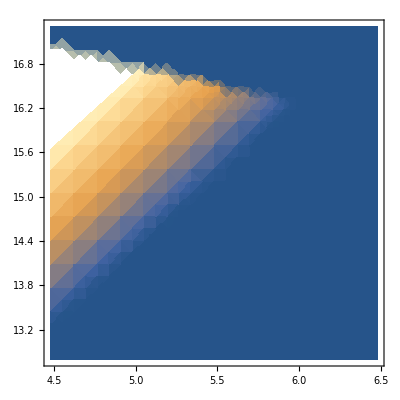

```mathematica
DensityPlot[testkinσinterpolate[["dσf"]][vχ,ω],{vχ,4.48,6.48},{ω,12.8,17.3}]
```

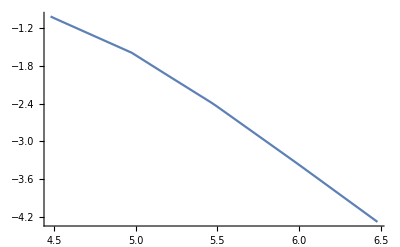

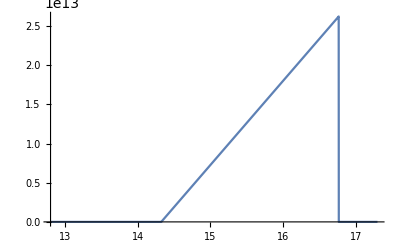

Because the grid of ω and vχ is unstructured, we get a simple linear fit. Try taking the max ωmax in the grid and just cutting off with a heaviside

```mathematica
Plot[testkinσinterpolate[["dσf"]][vχ,13],{vχ,4.48,6.48}]
Plot[testkinσinterpolate[["dσf"]][5,ω],{ω,12.8,17.3}]
Print["Because the grid of ω and vχ is unstructured, we get a simple linear fit. Try taking the max ωmax in the grid and just cutting off with a heaviside"]
```

#### Try interpolating over vχ and ω, but with a square grid - Doesn’t Work

```mathematica
GetvχandωListSquare[mχ_,vχ_,ωmax_,params_,n_:20]:=Module[{ωmin,ϵ,Interpointsω},
ωmin= "ωedgei"/.params;
(*ERmax = ωmax;*)

Interpointsω=10^Subdivide[Log10[ωmin],Log10[ωmax],n];
Table[{vχ,Interpointsω[[i]]},{i,n+1}]
]
```

```mathematica
InterpolatvχandωσdEReSquare[mχ_,vχ_:{10^-5,10^-2}"c"/.SIConstRepl,params_,m_:4,n_:20]:=Module[{ωmin,ωmax,Interpointsvχ,Interpointsvχandω,ϵ,InterdσTable,Interdσf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

(*local parameters*)
(*ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];*)
ωmin= "ωedgei"/.params;
ωmax =  1/(2"ℏ")mχ vχ[[2]]^2/.params;
Interpointsvχ=10^Subdivide[Log10[vχ[[1]]],Log10[vχ[[2]]],m];
Print[GetvχandωListSquare[mχ,Interpointsvχ[[1]],ωmax,params,n]];
Interpointsvχandω=Table[GetvχandωListSquare[mχ,Interpointsvχ[[i]],ωmax,params,n],{i,m+1}];
(*Interpointsvχandω=Table[GetvχandωListSquare[mχ,Interpointsvχ[[i]],ωmax,params,n],{i,m+1}];*)
(*Subdivide takes us slightly over ERmax, which throws errors. So subtract off a small fraction ϵ of ER max*)
(*Print[Interpointsvχandω[[1,1]][[1]]];
Print[Interpointsvχandω[[1,1]][[2]]];*)
(*Print[dσdERe[6.588699526066354*^12(1+ϵ),mχ,3000(1+ϵ),{params},"β"/.params]];
Print[dσdERe[Interpointsvχandω[[1,1]][[2]](1+ϵ),mχ,Interpointsvχandω[[1,1]][[1]],{params},"β"/.params]];*)
Print[dσdERe[Interpointsvχandω[[1,1]][[2]],mχ,Interpointsvχandω[[1,1]][[1]],{params},"β"/.params]HeavisideTheta[Interpointsvχandω[[1,1]][[2]]-ωmin]HeavisideTheta[( mχ/(2"ℏ")(Interpointsvχandω[[1,1]][[1]])^2/.params)-Interpointsvχandω[[1,1]][[2]]]];
InterdσTable=Table[{Interpointsvχandω[[i,j]],dσdERe[Interpointsvχandω[[i,j]][[2]],mχ,Interpointsvχandω[[i,j]][[1]],{params},"β"/.params]HeavisideTheta[Interpointsvχandω[[i,j]][[2]]-ωmin]HeavisideTheta[( mχ/(2"ℏ")(Interpointsvχandω[[i,j]][[1]])^2/.params)-Interpointsvχandω[[i,j]][[2]]]},{i,m+1},{j,n+1}];
Print[Flatten[InterdσTable,1]];
Interdσf=Interpolation[Flatten[InterdσTable,1]];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->Interpointsvχandω,"Interpointsvχ"->Interpointsvχ|>
]
```

```mathematica
testkinσinterpolateSquare=InterpolatvχandωσdEReSquare[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{10^-4,10^-2}"c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]],4,20]
```

{{30000,6.5887×10^12},{30000,1.10097×10^13},{30000,1.83972×10^13},{30000,3.07417×10^13},{30000,5.13693×10^13},{30000,8.5838×10^13},{30000,1.43435×10^14},{30000,2.3968×10^14},{30000,4.00505×10^14},{30000,6.69243×10^14},{30000,1.1183×10^15},{30000,1.86868×10^15},{30000,3.12257×10^15},{30000,5.21781×10^15},{30000,8.71895×10^15},{30000,1.45693×10^16},{30000,2.43453×10^16},{30000,4.0681×10^16},{30000,6.79779×10^16},{30000,1.13591×10^17},{30000,1.8981×10^17}}

0.128779

NIntegrate::inumr: The integrand -(0.0699144 Im[1/ϵMNum[0.000834741/(EnergyLoss`Private`z),EnergyLoss`Private`z,(«20»)/(«20»),{«1»}]])/(EnergyLoss`Private`z) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.0354795-0.0279276 ⅈ,0.0354795+0. ⅈ}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00032159492022796235086330718377922721629147417843341827392578125}. NIntegrate obtained 0.000117156 and 2.2645×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0003657868553803155195242209629657992309148539789021015167236328125}. NIntegrate obtained 0.000184102 and 1.80922×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.12196132850382213064222014509141445159912109375-0.54156685354676916268642291229238270738745584159086009742098706683 ⅈ}. NIntegrate obtained -0.000636687+0.00105807 ⅈ and 1.24195×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{{30000,6.5887×10^12},0.128779},{{30000,1.10097×10^13},0.0890861},{{30000,1.83972×10^13},0.0206049},{{30000,3.07417×10^13},0.},{{30000,5.13693×10^13},0.},{{30000,8.5838×10^13},0.},{{30000,1.43435×10^14},0.},{{30000,2.3968×10^14},0.},{{30000,4.00505×10^14},0.},{{30000,6.69243×10^14},0.},{{30000,1.1183×10^15},0.},{{30000,1.86868×10^15},0.},{{30000,3.12257×10^15},0.},{{30000,5.21781×10^15},0.},{{30000,8.71895×10^15},0.},{{30000,1.45693×10^16},0.},{{30000,2.43453×10^16},0.},{{30000,4.0681×10^16},0.},{{30000,6.79779×10^16},0.},{{30000,1.13591×10^17},0.},{{30000,1.8981×10^17},0.},{{30000 √10,6.5887×10^12},0.0279111},{{30000 √10,1.10097×10^13},0.0249931},{{30000 √10,1.83972×10^13},0.0220471},{{30000 √10,3.07417×10^13},0.0190356},{{30000 √10,5.13693×10^13},0.0158688},{{30000 √10,8.5838×10^13},0.0123041},{{30000 √10,1.43435×10^14},0.00741879},{{30000 √10,2.3968×10^14},0.},{{30000 √10,4.00505×10^14},0.},{{30000 √10,6.69243×10^14},0.},{{30000 √10,1.1183×10^15},0.},{{30000 √10,1.86868×10^15},0.},{{30000 √10,3.12257×10^15},0.},{{30000 √10,5.21781×10^15},0.},{{30000 √10,8.71895×10^15},0.},{{30000 √10,1.45693×10^16},0.},{{30000 √10,2.43453×10^16},0.},{{30000 √10,4.0681×10^16},0.},{{30000 √10,6.79779×10^16},0.},{{30000 √10,1.13591×10^17},0.},{{30000 √10,1.8981×10^17},0.},{{300000,6.5887×10^12},0.00414931},{{300000,1.10097×10^13},0.00386881},{{300000,1.83972×10^13},0.00359357},{{300000,3.07417×10^13},0.00332614},{{300000,5.13693×10^13},0.00307017},{{300000,8.5838×10^13},0.00283076},{{300000,1.43435×10^14},0.00261466},{{300000,2.3968×10^14},0.00242994},{{300000,4.00505×10^14},0.00228286},{{300000,6.69243×10^14},0.002162},{{300000,1.1183×10^15},0.00195456},{{300000,1.86868×10^15},0.000473946},{{300000,3.12257×10^15},0.},{{300000,5.21781×10^15},0.},{{300000,8.71895×10^15},0.},{{300000,1.45693×10^16},0.},{{300000,2.43453×10^16},0.},{{300000,4.0681×10^16},0.},{{300000,6.79779×10^16},0.},{{300000,1.13591×10^17},0.},{{300000,1.8981×10^17},0.},{{300000 √10,6.5887×10^12},0.000490234},{{300000 √10,1.10097×10^13},0.000462445},{{300000 √10,1.83972×10^13},0.000435401},{{300000 √10,3.07417×10^13},0.000409463},{{300000 √10,5.13693×10^13},0.00038523},{{300000 √10,8.5838×10^13},0.000363621},{{300000 √10,1.43435×10^14},0.000346061},{{300000 √10,2.3968×10^14},0.000334812},{{300000 √10,4.00505×10^14},0.000333572},{{300000 √10,6.69243×10^14},0.000348584},{{300000 √10,1.1183×10^15},0.000390397},{{300000 √10,1.86868×10^15},0.000474681},{{300000 √10,3.12257×10^15},0.000605796},{{300000 √10,5.21781×10^15},0.000781326},{{300000 √10,8.71895×10^15},0.000824436},{{300000 √10,1.45693×10^16},0.000319572},{{300000 √10,2.43453×10^16},0.+0. ⅈ},{{300000 √10,4.0681×10^16},0.+0. ⅈ},{{300000 √10,6.79779×10^16},0.+0. ⅈ},{{300000 √10,1.13591×10^17},0.+0. ⅈ},{{300000 √10,1.8981×10^17},0.+0. ⅈ},{{3000000,6.5887×10^12},0.0000536022},{{3000000,1.10097×10^13},0.0000530238},{{3000000,1.83972×10^13},0.0000501318},{{3000000,3.07417×10^13},0.0000476047},{{3000000,5.13693×10^13},0.0000452776},{{3000000,8.5838×10^13},0.0000432816},{{3000000,1.43435×10^14},0.0000418077},{{3000000,2.3968×10^14},0.0000411727},{{3000000,4.00505×10^14},0.00004192},{{3000000,6.69243×10^14},0.0000450281},{{3000000,1.1183×10^15},0.0000523279},{{3000000,1.86868×10^15},0.0000672103},{{3000000,3.12257×10^15},0.0000942808},{{3000000,5.21781×10^15},0.0001489},{{3000000,8.71895×10^15},0.000289498},{{3000000,1.45693×10^16},0.000555831},{{3000000,2.43453×10^16},0.000104805},{{3000000,4.0681×10^16},0.0000262153},{{3000000,6.79779×10^16},8.02963×10^-6},{{3000000,1.13591×10^17},2.59059×10^-6},{{3000000,1.8981×10^17},0.+0. ⅈ}}

<|dσf→InterpolatingFunction[…],dσTable→{{{{30000,6.5887×10^12},0.128779},{{30000,1.10097×10^13},0.0890861},{{30000,1.83972×10^13},0.0206049},{{30000,3.07417×10^13},0.},{{30000,5.13693×10^13},0.},{{30000,8.5838×10^13},0.},{{30000,1.43435×10^14},0.},{{30000,2.3968×10^14},0.},{{30000,4.00505×10^14},0.},{{30000,6.69243×10^14},0.},{{30000,1.1183×10^15},0.},{{30000,1.86868×10^15},0.},{{30000,3.12257×10^15},0.},{{30000,5.21781×10^15},0.},{{30000,8.71895×10^15},0.},{{30000,1.45693×10^16},0.},{{30000,2.43453×10^16},0.},{{30000,4.0681×10^16},0.},{{30000,6.79779×10^16},0.},{{30000,1.13591×10^17},0.},{{30000,1.8981×10^17},0.}},{{{30000 √10,6.5887×10^12},0.0279111},{{30000 √10,1.10097×10^13},0.0249931},{{30000 √10,1.83972×10^13},0.0220471},{{30000 √10,3.07417×10^13},0.0190356},{{30000 √10,5.13693×10^13},0.0158688},{{30000 √10,8.5838×10^13},0.0123041},{{30000 √10,1.43435×10^14},0.00741879},{{30000 √10,2.3968×10^14},0.},{{30000 √10,4.00505×10^14},0.},{{30000 √10,6.69243×10^14},0.},{{30000 √10,1.1183×10^15},0.},{{30000 √10,1.86868×10^15},0.},{{30000 √10,3.12257×10^15},0.},{{30000 √10,5.21781×10^15},0.},{{30000 √10,8.71895×10^15},0.},{{30000 √10,1.45693×10^16},0.},{{30000 √10,2.43453×10^16},0.},{{30000 √10,4.0681×10^16},0.},{{30000 √10,6.79779×10^16},0.},{{30000 √10,1.13591×10^17},0.},{{30000 √10,1.8981×10^17},0.}},{{{300000,6.5887×10^12},0.00414931},{{300000,1.10097×10^13},0.00386881},{{300000,1.83972×10^13},0.00359357},{{300000,3.07417×10^13},0.00332614},{{300000,5.13693×10^13},0.00307017},{{300000,8.5838×10^13},0.00283076},{{300000,1.43435×10^14},0.00261466},{{300000,2.3968×10^14},0.00242994},{{300000,4.00505×10^14},0.00228286},{{300000,6.69243×10^14},0.002162},{{300000,1.1183×10^15},0.00195456},{{300000,1.86868×10^15},0.000473946},{{300000,3.12257×10^15},0.},{{300000,5.21781×10^15},0.},{{300000,8.71895×10^15},0.},{{300000,1.45693×10^16},0.},{{300000,2.43453×10^16},0.},{{300000,4.0681×10^16},0.},{{300000,6.79779×10^16},0.},{{300000,1.13591×10^17},0.},{{300000,1.8981×10^17},0.}},{{{300000 √10,6.5887×10^12},0.000490234},{{300000 √10,1.10097×10^13},0.000462445},{{300000 √10,1.83972×10^13},0.000435401},{{300000 √10,3.07417×10^13},0.000409463},{{300000 √10,5.13693×10^13},0.00038523},{{300000 √10,8.5838×10^13},0.000363621},{{300000 √10,1.43435×10^14},0.000346061},{{300000 √10,2.3968×10^14},0.000334812},{{300000 √10,4.00505×10^14},0.000333572},{{300000 √10,6.69243×10^14},0.000348584},{{300000 √10,1.1183×10^15},0.000390397},{{300000 √10,1.86868×10^15},0.000474681},{{300000 √10,3.12257×10^15},0.000605796},{{300000 √10,5.21781×10^15},0.000781326},{{300000 √10,8.71895×10^15},0.000824436},{{300000 √10,1.45693×10^16},0.000319572},{{300000 √10,2.43453×10^16},0.+0. ⅈ},{{300000 √10,4.0681×10^16},0.+0. ⅈ},{{300000 √10,6.79779×10^16},0.+0. ⅈ},{{300000 √10,1.13591×10^17},0.+0. ⅈ},{{300000 √10,1.8981×10^17},0.+0. ⅈ}},{{{3000000,6.5887×10^12},0.0000536022},{{3000000,1.10097×10^13},0.0000530238},{{3000000,1.83972×10^13},0.0000501318},{{3000000,3.07417×10^13},0.0000476047},{{3000000,5.13693×10^13},0.0000452776},{{3000000,8.5838×10^13},0.0000432816},{{3000000,1.43435×10^14},0.0000418077},{{3000000,2.3968×10^14},0.0000411727},{{3000000,4.00505×10^14},0.00004192},{{3000000,6.69243×10^14},0.0000450281},{{3000000,1.1183×10^15},0.0000523279},{{3000000,1.86868×10^15},0.0000672103},{{3000000,3.12257×10^15},0.0000942808},{{3000000,5.21781×10^15},0.0001489},{{3000000,8.71895×10^15},0.000289498},{{3000000,1.45693×10^16},0.000555831},{{3000000,2.43453×10^16},0.000104805},{{3000000,4.0681×10^16},0.0000262153},{{3000000,6.79779×10^16},8.02963×10^-6},{{3000000,1.13591×10^17},2.59059×10^-6},{{3000000,1.8981×10^17},0.+0. ⅈ}}},Interpoints→{{{30000,6.5887×10^12},{30000,1.10097×10^13},{30000,1.83972×10^13},{30000,3.07417×10^13},{30000,5.13693×10^13},{30000,8.5838×10^13},{30000,1.43435×10^14},{30000,2.3968×10^14},{30000,4.00505×10^14},{30000,6.69243×10^14},{30000,1.1183×10^15},{30000,1.86868×10^15},{30000,3.12257×10^15},{30000,5.21781×10^15},{30000,8.71895×10^15},{30000,1.45693×10^16},{30000,2.43453×10^16},{30000,4.0681×10^16},{30000,6.79779×10^16},{30000,1.13591×10^17},{30000,1.8981×10^17}},{{30000 √10,6.5887×10^12},{30000 √10,1.10097×10^13},{30000 √10,1.83972×10^13},{30000 √10,3.07417×10^13},{30000 √10,5.13693×10^13},{30000 √10,8.5838×10^13},{30000 √10,1.43435×10^14},{30000 √10,2.3968×10^14},{30000 √10,4.00505×10^14},{30000 √10,6.69243×10^14},{30000 √10,1.1183×10^15},{30000 √10,1.86868×10^15},{30000 √10,3.12257×10^15},{30000 √10,5.21781×10^15},{30000 √10,8.71895×10^15},{30000 √10,1.45693×10^16},{30000 √10,2.43453×10^16},{30000 √10,4.0681×10^16},{30000 √10,6.79779×10^16},{30000 √10,1.13591×10^17},{30000 √10,1.8981×10^17}},{{300000,6.5887×10^12},{300000,1.10097×10^13},{300000,1.83972×10^13},{300000,3.07417×10^13},{300000,5.13693×10^13},{300000,8.5838×10^13},{300000,1.43435×10^14},{300000,2.3968×10^14},{300000,4.00505×10^14},{300000,6.69243×10^14},{300000,1.1183×10^15},{300000,1.86868×10^15},{300000,3.12257×10^15},{300000,5.21781×10^15},{300000,8.71895×10^15},{300000,1.45693×10^16},{300000,2.43453×10^16},{300000,4.0681×10^16},{300000,6.79779×10^16},{300000,1.13591×10^17},{300000,1.8981×10^17}},{{300000 √10,6.5887×10^12},{300000 √10,1.10097×10^13},{300000 √10,1.83972×10^13},{300000 √10,3.07417×10^13},{300000 √10,5.13693×10^13},{300000 √10,8.5838×10^13},{300000 √10,1.43435×10^14},{300000 √10,2.3968×10^14},{300000 √10,4.00505×10^14},{300000 √10,6.69243×10^14},{300000 √10,1.1183×10^15},{300000 √10,1.86868×10^15},{300000 √10,3.12257×10^15},{300000 √10,5.21781×10^15},{300000 √10,8.71895×10^15},{300000 √10,1.45693×10^16},{300000 √10,2.43453×10^16},{300000 √10,4.0681×10^16},{300000 √10,6.79779×10^16},{300000 √10,1.13591×10^17},{300000 √10,1.8981×10^17}},{{3000000,6.5887×10^12},{3000000,1.10097×10^13},{3000000,1.83972×10^13},{3000000,3.07417×10^13},{3000000,5.13693×10^13},{3000000,8.5838×10^13},{3000000,1.43435×10^14},{3000000,2.3968×10^14},{3000000,4.00505×10^14},{3000000,6.69243×10^14},{3000000,1.1183×10^15},{3000000,1.86868×10^15},{3000000,3.12257×10^15},{3000000,5.21781×10^15},{3000000,8.71895×10^15},{3000000,1.45693×10^16},{3000000,2.43453×10^16},{3000000,4.0681×10^16},{3000000,6.79779×10^16},{3000000,1.13591×10^17},{3000000,1.8981×10^17}}},Interpointsvχ→{30000,30000 √10,300000,300000 √10,3000000}|>

InterpolatingFunction::dmval: Input value {4.48014,12.8003} lies outside the range of data in the interpolating function. Extrapolation will be used.

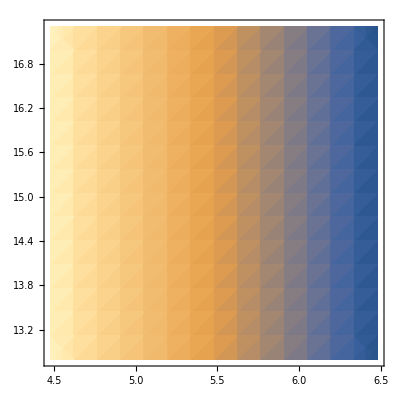

```mathematica
DensityPlot[testkinσinterpolateSquare[["dσf"]][vχ,ω],{vχ,4.48,6.48},{ω,12.8,17.3}]
```

InterpolatingFunction::dmval: Input value {4.48004,13} lies outside the range of data in the interpolating function. Extrapolation will be used.

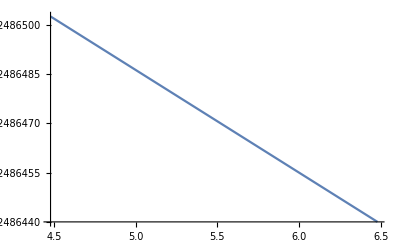

InterpolatingFunction::dmval: Input value {5,13.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

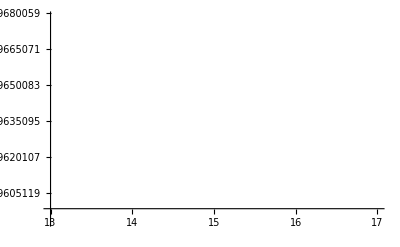

```mathematica
Plot[testkinσinterpolateSquare[["dσf"]][vχ,13],{vχ,4.48,6.48}]
Plot[testkinσinterpolateSquare[["dσf"]][5,ω],{ω,13,17}]
```

#### Interpolate with vχ and ξ

Psuedo-code:

We want to use ξ ∈ [0,1) with ω(ξ) = ω_min+ξ(ω_max-ω_min)
This should eleviate both issues we were having before, it interpolates only over the region of integration (so we get variation with ω and no issues with Heavisides) and also is a square grid (so no reduced order interpolations)

```mathematica
testkinσinterpolateξmeosc2higherres=InterpolatevχandωσdEReξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-4,10^-2}"c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]],5,60,10^-4,4];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000122581875730450894405008932519507425240590237081050872802734375}. NIntegrate obtained 0.00020251 and 3.43551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0002551760996913700316776445198296840999319101683795452117919921875}. NIntegrate obtained 0.00010951 and 2.80601×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0001781783644222577315413026666224283189876587130129337310791015625}. NIntegrate obtained 0.000139236 and 7.39518×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

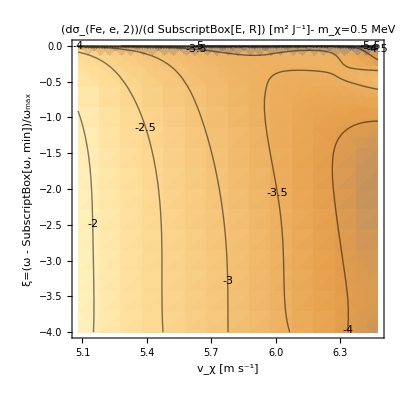

Compare to the above plot, checking the ω scale

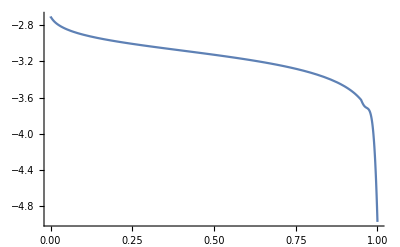

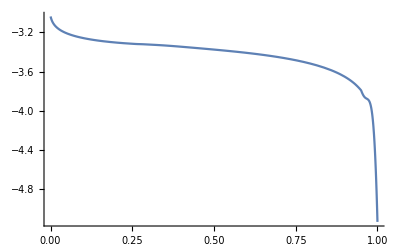

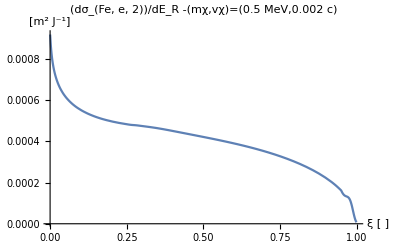

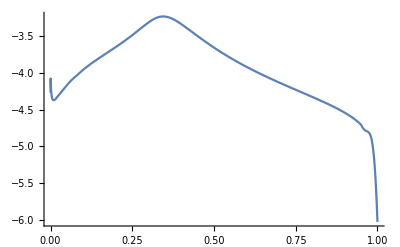

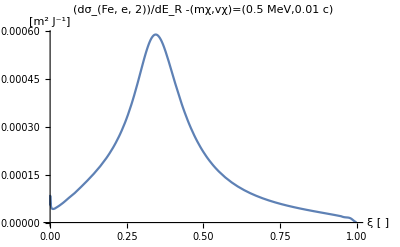

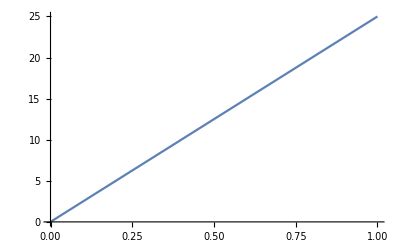

```mathematica
vχbounds=testkinσinterpolateξmeosc2higherres[["vχ"]];
ξbounds=testkinσinterpolateξmeosc2higherres[["ξ"]];
Show[{DensityPlot[testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},PlotLabel->"(dσ_(Fe, e, 2))/(d SubscriptBox[E, R]) [m^2 J^-1]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
Print["Compare to the above plot, checking the ω scale"]
Plot[testkinσinterpolateξmeosc2higherres[["dσf"]][5.6,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All]
Plot[testkinσinterpolateξmeosc2higherres[["dσf"]][5.8,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All]
Plot[10^testkinσinterpolateξmeosc2higherres[["dσf"]][5.8,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All,PlotLabel->"(dσ_(Fe, e, 2))/dE_R -(mχ,vχ)=(0.5 MeV,0.002 c)",AxesLabel->{"ξ [ ]","[m^2 J^-1]"}]
Plot[testkinσinterpolateξmeosc2higherres[["dσf"]][vχbounds[[2]],Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All]
Plot[10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχbounds[[2]],Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All,PlotLabel->"(dσ_(Fe, e, 2))/dE_R -(mχ,vχ)=(0.5 MeV,0.01 c)",AxesLabel->{"ξ [ ]","[m^2 J^-1]"}]
Plot[(("ℏ")/("JpereV")/.SIConstRepl)ωofξandvχ[ξ,testkinσinterpolateξmeosc2higherres[["ωmin"]],10^vχbounds[[2]],testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
(*Plot[(("ℏ")/("JpereV")/.SIConstRepl)ξofωandvχ[ω,testkinσinterpolateξmeosc2higherres[["ωmin"]],10^vχbounds[[2]],testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]],{ω,10^ξbounds[[1]],10^ξbounds[[2]]}]*)
```

```mathematica
("JpereV"/.SIConstRepl)
```

1.602×10^-19

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000141826}. NIntegrate obtained 0.000132359 and 2.63987×10^-6 for the integral and error estimates.

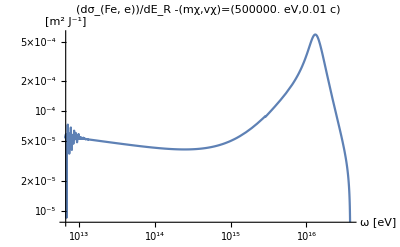

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000149062}. NIntegrate obtained 0.000143482 and 1.97166×10^-6 for the integral and error estimates.

-Graphics-

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp,ERmintemp},
mχtemp = testkinσinterpolateξmeosc2higherres[["mχ"]];
vχtemp = 10^testkinσinterpolateξmeosc2higherres[["vχ"]][[2]];
ERmaxtemp = ωmaxofvχ[10^vχbounds[[2]],testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]];
ERmintemp = testkinσinterpolateξmeosc2higherres[["ωmin"]];
Print[LogLogPlot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]];
Plot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000334144122406762993635932768032859030427061952650547027587890625}. NIntegrate obtained 0.000097441 and 1.80677×10^-9 for the integral and error estimates.

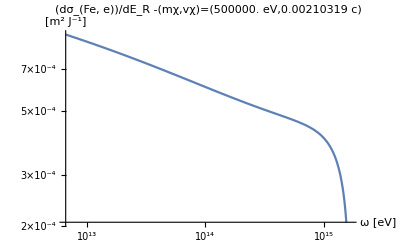

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0003356319043151438107400706678529189730397774837911128997802734375}. NIntegrate obtained 0.0000978685 and 2.73029×10^-9 for the integral and error estimates.

-Graphics-

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp,ERmintemp},
mχtemp = testkinσinterpolateξmeosc2higherres[["mχ"]];
vχtemp = 10^(5.8);
ERmaxtemp = ωmaxofvχ[vχtemp,testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]];
ERmintemp = testkinσinterpolateξmeosc2higherres[["ωmin"]];
Print[LogLogPlot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]];
Plot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

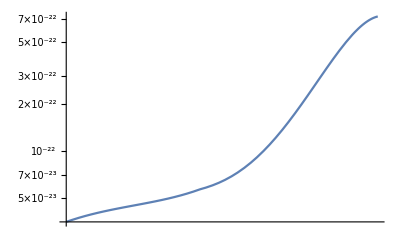

```mathematica
LogLogPlot[10^testkinσinterpolateξmeosc2higherres["σf"][vχ],{vχ,vχbounds[[1]],vχbounds[[2]]}]
```

#### Recoil Energy Probability

It looks like we are off by an order 1 factor if we try to normalize the distribution as in the notes. Possibly from the interpolation. Note that The distribution includes a factor of ℏ (ωmax-ωmin) as we are using ξ rather than E_R as a variable

4.27038×10^11 10^(-7.79507+InterpolatingFunction[…][6.35,Log[ξ]/Log[10]])

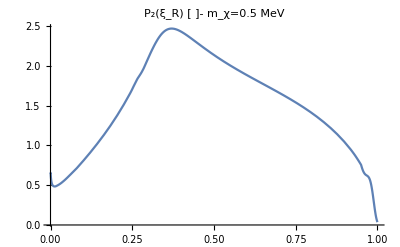

1.52955

```mathematica
Print["It looks like we are off by an order 1 factor if we try to normalize the distribution as in the notes. Possibly from the interpolation. Note that The distribution includes a factor of ℏ (ωmax-ωmin) as we are using ξ rather than E_R as a variable"]
10^Log10[(("ne"/.FeλeDictOscillators[[2]]["fitparams"][[1]])10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])(ωmaxofvχ[10^(vχ),testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]]-testkinσinterpolateξmeosc2higherres[["ωmin"]])"ℏ"/.testkinσinterpolateξmeosc2higherres[["params"]]]/.vχ->6.35
Plot[%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(ξ_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}]
NIntegrate[%%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
```

Normalize the distribution by 1 (divide by total cross-section)

2.2191×10^-18 10^(InterpolatingFunction[…][6.34898,Log[ξ]/Log[10]])

4.96885×10^-22

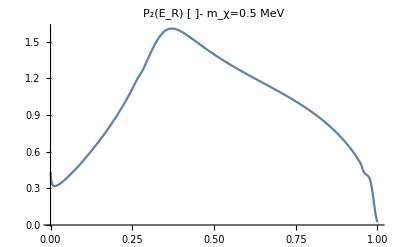

1.

```mathematica
Print["Normalize the distribution by 1 (divide by total cross-section)"]
10^Log10[10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]](ωmaxofvχ[10^(vχ),testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]]-testkinσinterpolateξmeosc2higherres[["ωmin"]])"ℏ"/.testkinσinterpolateξmeosc2higherres[["params"]]]/.vχ->1.25 vχbounds[[1]]
NIntegrate[%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
Plot[(%%)/%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(E_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}]
NIntegrate[(%%%)/(%%),{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
```

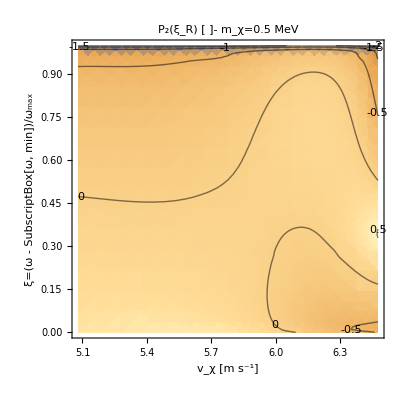

```mathematica
Show[{DensityPlot[Log10[(10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]])/NIntegrate[10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξt]],{ξt,10^ξbounds[[1]],10^ξbounds[[2]]}]],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(ξ_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[Log10[(10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]])/NIntegrate[10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξt]],{ξt,10^ξbounds[[1]],10^ξbounds[[2]]}]],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
```

```mathematica
Print["Peak v_χ~ 10^6.3 = ",N[10^6.3]," [ms^-1]"]
Print["vF = ","vF"/.testkinσinterpolateξmeosc2higherres[["params"]]," [ms^-1]"]
```

Peak v_χ~ 10^6.3 = 1.99526×10^6 [ms^-1]

vF = 2.06517×10^6 [ms^-1]

```mathematica
Ptest[vχ_,ξ_]:=(10^testkinσinterpolateξmeosc2higherres[["dσf"]][#1,#2]/NIntegrate[10^testkinσinterpolateξmeosc2higherres[["dσf"]][#1,ξt],{ξt,ξbounds[[1]],ξbounds[[2]]}])&[vχ,ξ]
```

```mathematica
Ptest[vχbounds[[2]]0.99,-3]
```

0.174541

### Nuclear - Unit Test - Get plots for λ, σ, and dσdER

#### dσdER

```mathematica
Print["Get ω_max and ω_min for nuclear"]
qω =ℏ √((2mN ω)/ℏ)
qpm = m v + √(2 m (1/2 m v^2 - ω ℏ))
Solve[qpm - qω== 0,ω]//Simplify
Print["These are precisely the bounds we found for the nergy loss rate."]
```

Get ω_max and ω_min for nuclear

√2 √((mN ω)/ℏ) ℏ

m v+√2 √(m ((m v^2)/2-ω ℏ))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ω→0},{ω→(2 m^2 mN v^2)/((m+mN)^2 ℏ)}}

These are precisely the bounds we found for the nergy loss rate.

{-4,-Log[10000/9999]/Log[10]}

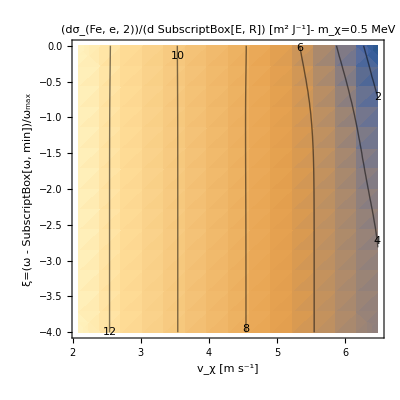

```mathematica
kinσinterPξNuc=InterpolatevχandωσdERNucξ[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-7,10^-2}"c"/.SIConstRepl,FeNucCoeffs,SIConstRepl,5,60,10^-4];
vχbounds=kinσinterPξNuc[["vχ"]];
ξbounds=kinσinterPξNuc[["ξ"]]
Show[{DensityPlot[kinσinterPξNuc[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},PlotLabel->"(dσ_(Fe, e, 2))/(d SubscriptBox[E, R]) [m^2 J^-1]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[kinσinterPξNuc[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
```

#### Nuclear Probability Distribution

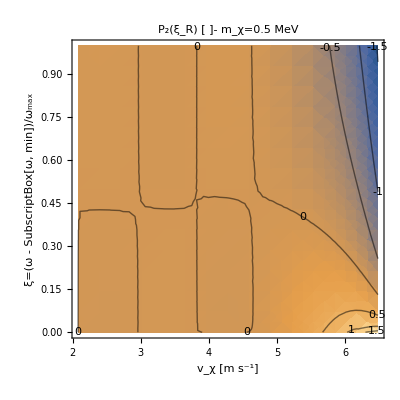

```mathematica
Show[{DensityPlot[Log10[(10^kinσinterPξNuc[["dσf"]][vχ,Log10[ξ]])/NIntegrate[10^kinσinterPξNuc[["dσf"]][vχ,Log10[ξt]],{ξt,10^ξbounds[[1]],10^ξbounds[[2]]}]],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(ξ_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[Log10[(10^kinσinterPξNuc[["dσf"]][vχ,Log10[ξ]])/NIntegrate[10^kinσinterPξNuc[["dσf"]][vχ,Log10[ξt]],{ξt,10^ξbounds[[1]],10^ξbounds[[2]]}]],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
```

10^(InterpolatingFunction[…][4.35,Log[ξ]/Log[10]])

2.44294×10^8

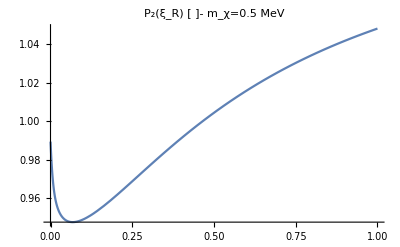

1.

```mathematica
10^kinσinterPξNuc[["dσf"]][vχ,Log10[ξ]]/.vχ->4.35
NIntegrate[%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
Plot[(%%)/%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(ξ_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}]
NIntegrate[(%%%)/(%%),{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
```

10^(InterpolatingFunction[…][4.35,Log[ξ]/Log[10]])

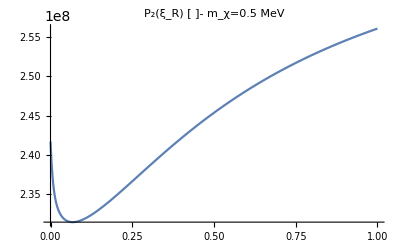

2.44294×10^8

```mathematica
10^kinσinterPξNuc[["dσf"]][vχ,Log10[ξ]]/.vχ->4.35
Plot[%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(ξ_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}]
NIntegrate[%%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
```

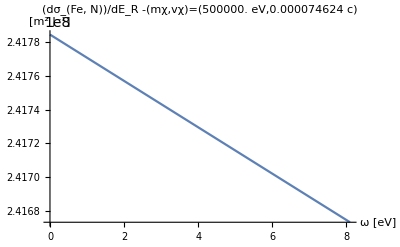

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp =  10^4.35 ;
ERmaxtemp =ωmaxNuc[vχtemp,mχtemp,"mN"/.FeNucCoeffs,SIConstRepl];Plot[dσdERNuc0[ω,mχtemp,vχtemp,FeNucCoeffs,SIConstRepl],{ω,10^-4 ERmaxtemp,ERmaxtemp},PlotRange->All,PlotLabel->StringForm["(dσ_(Fe, N))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

#### σ

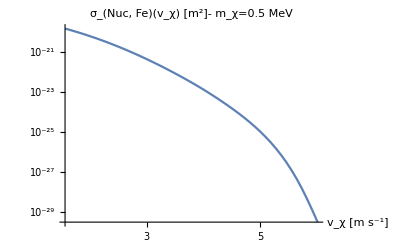

```mathematica
LogLogPlot[("ℏ"/.SIConstRepl) ωmaxNuc[vχ,kinσinterPξNuc[["mχ"]],"mN"/.FeNucCoeffs,SIConstRepl] NIntegrate[10^kinσinterPξNuc[["dσf"]][vχ,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}],{vχ,vχbounds[[1]],vχbounds[[2]]},PlotLabel->"σ_(Nuc, Fe)(v_χ) [m^2]- m_χ=0.5 MeV",PlotRange->All,AxesLabel->{"v_χ [m s^-1]" }]
```

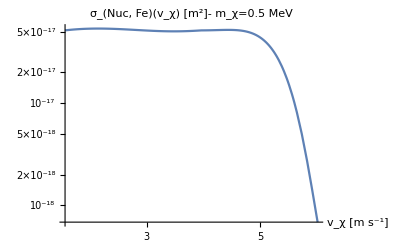

```mathematica
LogLogPlot[("ℏ"/.SIConstRepl) ωmaxNuc[10^vχ,kinσinterPξNuc[["mχ"]],"mN"/.FeNucCoeffs,SIConstRepl] NIntegrate[10^kinσinterPξNuc[["dσf"]][vχ,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}],{vχ,vχbounds[[1]],vχbounds[[2]]},PlotLabel->"σ_(Nuc, Fe)(v_χ) [m^2]- m_χ=0.5 MeV",PlotRange->All,AxesLabel->{"v_χ [m s^-1]" }]
```

```mathematica
Print["Boundary where energy transfer distribution becomes approximately constant is given approximately by the energy transfer:"]
1/("JpereV"/.SIConstRepl)("ℏ"/.SIConstRepl) ωmaxNuc[vχ,kinσinterPξNuc[["mχ"]],"mN"/.FeNucCoeffs,SIConstRepl]/.vχ->10^5
Print["The corresponding target momentum is then q = √(2 SubscriptBox[m, N ] SubscriptBox[E, R])"]
(2 %% (("c")^2/("JpereV")"mN"/.FeNucCoeffs/.SIConstRepl))^(1/2)
```

Boundary where energy transfer distribution becomes approximately constant is given approximately by the energy transfer:

0.0000265919

The corresponding target momentum is then q = √(2 SubscriptBox[m, N ] SubscriptBox[E, R])

5.76028×10^-6

#### Unit test σ interpolation

```mathematica
(*InterpolatevχandωσdERNucξ[mχ_:0.5 10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl,vχ_:{4 10^-4,10^-2}"c"/.Constants`SIConstRepl,FFcoeffs_,params_,m_:5,n_:60,ϵ_:10^-4]:=Module[{ωmin,mN,Interpointsvχ,Interpointsvχandξ,InterdσTable,Interdσf,InterσTable,Interσf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

ωmin=0;
mN = "mN"/.FFcoeffs;

Interpointsvχ=10^Subdivide[Log10[vχ[[1]]],Log10[vχ[[2]]],m];
Interpointsvχandξ=SortBy[Table[GetvχandξList[Interpointsvχ[[i]],n,ϵ,True],{i,m+1}],Last];

(*Interpolate to get dσ/dER*)
InterdσTable=Table[{Interpointsvχandξ[[i,j]],dσdERNuc0[ωofξ[Interpointsvχandξ[[i,j]][[2]],ωmin,ωmaxNuc[Interpointsvχandξ[[i,j]][[1]],mχ,mN,params]],mχ,Interpointsvχandξ[[i,j]][[1]],FFcoeffs,params]},{i,m+1},{j,n+1}];
Interdσf=Interpolation[Flatten[Log10[InterdσTable],1],InterpolationOrder->4];

(*Interpolate to get σ*)
InterσTable =Table[{Interpointsvχ[[i]],NIntegrate[10^Interdσf[Log10[Interpointsvχ[[i]]],Log10[ξ]],{ξ,ϵ,1-ϵ}]},{i,m+1}];
Interσf = Interpolation[Log10[InterdσTable],InterpolationOrder->4];

<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->Interpointsvχandξ,"σf"->Interσf,"σTable"->InterσTable,"Interpointsvχ"->Interpointsvχ,"mχ"->mχ,"vχ"->Log10[vχ],"ξ"->Log10[{ϵ,1-ϵ}],"NucleusParams"->FFcoeffs,"params"->params,"ωmin"->ωmin|>
]*)
```

-Graphics-

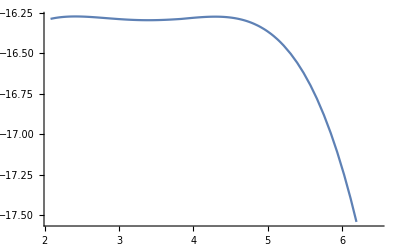

```mathematica
kinσinterPξNuc=InterpolatevχandωσdERNucξ[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-7,10^-2}"c"/.SIConstRepl,FeNucCoeffs,SIConstRepl,5,60,10^-4];
vχbounds=kinσinterPξNuc[["vχ"]];
ξbounds=kinσinterPξNuc[["ξ"]];
Show[{DensityPlot[kinσinterPξNuc[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},PlotLabel->"(dσ_(Fe, e, 2))/(d SubscriptBox[E, R]) [m^2 J^-1]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[kinσinterPξNuc[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
Plot[kinσinterPξNuc["σf"][vχ],{vχ,vχbounds[[1]],vχbounds[[2]]}]
```

```mathematica
Plot[kinσinterPξNuc["σf"][vχ],{vχ,vχbounds[[1]],vχbounds[[2]]}]
LogLogPlot[("ℏ"/.SIConstRepl) ωmaxNuc[10^vχ,kinσinterPξNuc[["mχ"]],"mN"/.FeNucCoeffs,SIConstRepl] NIntegrate[10^kinσinterPξNuc[["dσf"]][vχ,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}],{vχ,vχbounds[[1]],vχbounds[[2]]},PlotLabel->"σ_(Nuc, Fe)(v_χ) [m^2]- m_χ=0.5 MeV",PlotRange->All,AxesLabel->{"v_χ [m s^-1]" }]
```

-Graphics-

-Graphics-

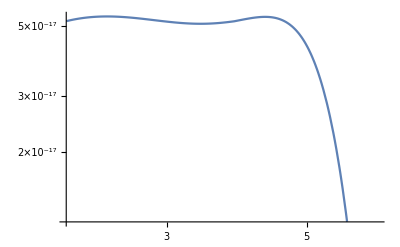

```mathematica
LogLogPlot[10^kinσinterPξNuc["σf"][vχ],{vχ,vχbounds[[1]],vχbounds[[2]]}]
```

### Get Cross-sections - All materials and Processes

#### Electronic

```mathematica
FeσDicteme=InterpolatevχandωσdEReξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-4,10^-2}"c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]],5,60,10^-4,4];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000122581875730450894405008932519507425240590237081050872802734375}. NIntegrate obtained 0.00020251 and 3.43551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0002551760996913700316776445198296840999319101683795452117919921875}. NIntegrate obtained 0.00010951 and 2.80601×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0001781783644222577315413026666224283189876587130129337310791015625}. NIntegrate obtained 0.000139236 and 7.39518×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
vχbounds=FeσDicteme[["vχ"]]
ξbounds=FeσDicteme[["ξ"]];
Show[{DensityPlot[FeσDicteme[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},PlotLabel->"(dσ_(Fe, e, 2))/(d SubscriptBox[E, R]) [m^2 J^-1]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[FeσDicteme[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
```

{Log[120000]/Log[10],Log[3000000]/Log[10]}

-Graphics-

```mathematica
FeσDicteme=Table[InterpolatevχandωσdEReξdebug[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,FeλeDictOscillators[[i]][["fitparams"]][[1]],10,60,10^-4,4,True],{i,Length[FeλeDictOscillators]}]
```

General::munfl: Exp[-817.073] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-952.495] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1110.39] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00199143993077914994820065697211930455523543059825897216796875}. NIntegrate obtained 0.112636 and 3.48157×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01825}. NIntegrate obtained 0.117065 and 1.21313×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0021145656449017874618789836205223764409311115741729736328125}. NIntegrate obtained 0.122192 and 2.77484×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
?SaveIt
```

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictme",FeσDicteme]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\dsigmadER\FeσDictme.dat

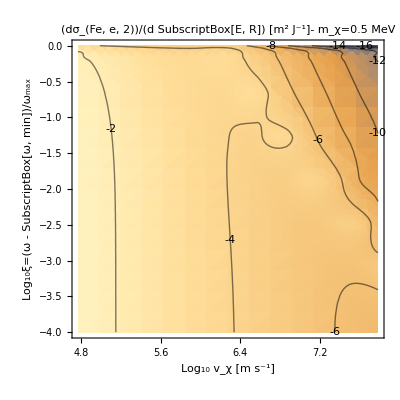

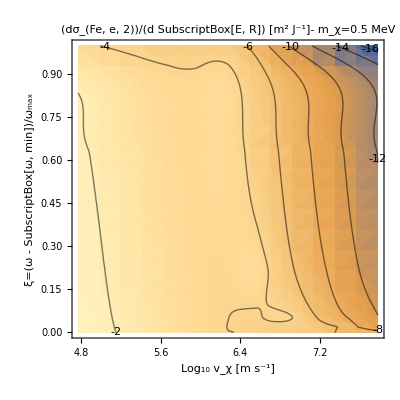

-Graphics-

-Graphics-

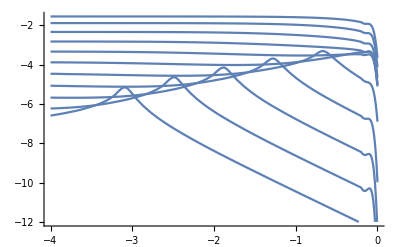

```mathematica
vχbounds=FeσDicteme[[2]][["vχ"]];
ξbounds=FeσDicteme[[2]][["ξ"]];
Show[{DensityPlot[FeσDicteme[[2]][["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},PlotLabel->"(dσ_(Fe, e, 2))/(d SubscriptBox[E, R]) [m^2 J^-1]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"Log_10 v_χ [m s^-1]" ,"Log_10ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[FeσDicteme[[2]][["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
Show[{DensityPlot[FeσDicteme[[2]][["dσf"]][vχ,Log10[ξ]],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"(dσ_(Fe, e, 2))/(d SubscriptBox[E, R]) [m^2 J^-1]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"Log_10 v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[FeσDicteme[[2]][["dσf"]][vχ,Log10[ξ]],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
Show[Table[Plot[FeσDicteme[[i]][["σf"]][vχ],{vχ,FeσDicteme[[i]][["vχ"]][[1]],FeσDicteme[[i]]["vχ"][[2]]},PlotRange->{{FeσDicteme[[2]]["vχ"][[1]],FeσDicteme[[i]]["vχ"][[2]]},{-35,-20}},PlotLabels->i,PlotLabel->"σ_Fe - Per Oscillator",AxesLabel->{"Log10[v_χ] [ms^-1]","[m^2]"}],{i,Length[FeσDicteme]}]]
Show[Table[Plot[Log10["ne"/.FeσDicteme[[i]][["params"]]]+FeσDicteme[[i]][["σf"]][vχ],{vχ,FeσDicteme[[i]][["vχ"]][[1]],FeσDicteme[[i]]["vχ"][[2]]},PlotRange->{{FeσDicteme[[2]]["vχ"][[1]],FeσDicteme[[i]]["vχ"][[2]]},{1,10}} ,PlotLabels->i,PlotLabel->"λ_Fe^-1 - Per Oscillator",AxesLabel->{"Log10[v_χ] [ms^-1]","[m^-1]"}],{i,Length[FeσDicteme]}]]
(*Show[Table[Plot[FeσDicteme[[i]][["dσf"]][FeσDicteme[[i]][["vχ"]][[]],ξ],{ξ,ξbounds[[1]],ξbounds[[2]]}],{i,Length[FeσDicteme]}]]*)
Show[Table[Plot[FeσDicteme[[2]][["dσf"]][Log10[FeσDicteme[[2]][["Interpointsvχ"]][[i]]],ξ],{ξ,ξbounds[[1]],ξbounds[[2]]},PlotRange->{0,-12}],{i,Length[FeσDicteme[[2]][["Interpointsvχ"]]]}]]
```

```mathematica
SiO2σDicteme=Table[InterpolatevχandωσdEReξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,ReplaceParams[SiO2λeDictOscillators[[i]][["fitparams"]][[1]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],10,60,10^-4,4,True],{i,Length[SiO2λeDictOscillators]}];
```

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-743.533] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01627}. NIntegrate obtained 0.0348346 and 6.42727×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00185232}. NIntegrate obtained 1.47436×10^-7 and 1.52427×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000380795}. NIntegrate obtained 1.32112×10^-8 and 1.34235×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
SaveIt[NotebookDirectory[]<>"SiO2σDictme",SiO2σDicteme]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\dsigmadER\SiO2σDictme.dat

```mathematica
Show[Table[Plot[SiO2σDicteme[[i]][["σf"]][vχ],{vχ,SiO2σDicteme[[i]][["vχ"]][[1]],SiO2σDicteme[[i]]["vχ"][[2]]},PlotRange->{{SiO2σDicteme[[2]]["vχ"][[1]],SiO2σDicteme[[i]]["vχ"][[2]]},{-25,-20}},PlotLabels->i,PlotLabel->"σ_SiO2 - Per Oscillator",AxesLabel->{"Log10[v_χ] [ms^-1]","[m^2]"}],{i,Length[SiO2σDicteme]}]]
Show[Table[Plot[Log10["ne"/.SiO2σDicteme[[i]][["params"]]]+SiO2σDicteme[[i]][["σf"]][vχ],{vχ,SiO2σDicteme[[i]][["vχ"]][[1]],SiO2σDicteme[[i]]["vχ"][[2]]},PlotRange->{{SiO2σDicteme[[2]]["vχ"][[1]],SiO2σDicteme[[i]]["vχ"][[2]]},{6,10}} ,PlotLabels->i,PlotLabel->"λ_SiO2^-1 - Per Oscillator",AxesLabel->{"Log10[v_χ] [ms^-1]","[m^-1]"}],{i,Length[SiO2σDicteme]}]]
```

-Graphics-

-Graphics-

```mathematica
MgOσDicteme=Table[InterpolatevχandωσdEReξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,ReplaceParams[MgOλeDictOscillators[[i]][["fitparams"]][[1]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],5,60,10^-4,4,True],{i,Length[MgOλeDictOscillators]}];
```

General::munfl: Exp[-713.408] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-780.205] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-858.084] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.02953}. NIntegrate obtained 0.00476182 and 1.546×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.03142}. NIntegrate obtained 0.00363888 and 9.56125×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3.2126}. NIntegrate obtained 0.0000841753 and 1.27156×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
SaveIt[NotebookDirectory[]<>"MgOσDictme",MgOσDicteme]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\dsigmadER\MgOσDictme.dat

```mathematica
Show[Table[Plot[MgOσDicteme[[i]][["σf"]][vχ],{vχ,MgOσDicteme[[i]][["vχ"]][[1]],MgOσDicteme[[i]]["vχ"][[2]]},PlotRange->{{MgOσDicteme[[2]]["vχ"][[1]],MgOσDicteme[[i]]["vχ"][[2]]},{-25,-21}},PlotLabels->i,PlotLabel->"σ_MgO - Per Oscillator",AxesLabel->{"Log10[v_χ] [ms^-1]","[m^2]"}],{i,Length[MgOσDicteme]}]]
Show[Table[Plot[Log10["ne"/.MgOσDicteme[[i]][["params"]]]+MgOσDicteme[[i]][["σf"]][vχ],{vχ,MgOσDicteme[[i]][["vχ"]][[1]],MgOσDicteme[[i]]["vχ"][[2]]},PlotRange->{{MgOσDicteme[[2]]["vχ"][[1]],MgOσDicteme[[i]]["vχ"][[2]]},{4,9}} ,PlotLabels->i,PlotLabel->"λ_MgO^-1 - Per Oscillator",AxesLabel->{"Log10[v_χ] [ms^-1]","[m^-1]"}],{i,Length[MgOσDicteme]}]]
```

-Graphics-

-Graphics-

#### Nuclear

```mathematica
FeσDictNucme=InterpolatevχandωσdERNucξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-7,2 10^-1}"c"/.SIConstRepl,FeNucCoeffs,SIConstRepl,20,60,10^-4];
```

General::munfl: Exp[-790.662] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-921.843] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1074.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
SiσDictNucme=InterpolatevχandωσdERNucξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-7,2 10^-1}"c"/.SIConstRepl,SiNucCoeffs,SIConstRepl,20,60,10^-4];
```

General::munfl: Exp[-720.591] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-840.147] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-979.537] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
MgσDictNucme=InterpolatevχandωσdERNucξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-7,2 10^-1}"c"/.SIConstRepl,MgNucCoeffs,SIConstRepl,20,60,10^-4];
```

General::munfl: Exp[-815.124] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-950.363] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1108.04] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
OσDictNucme=InterpolatevχandωσdERNucξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-7,2 10^-1}"c"/.SIConstRepl,ONucCoeffs,SIConstRepl,20,60,10^-4];
```

General::munfl: Exp[-729.117] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-850.086] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-991.126] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNucme",FeσDictNucme]
SaveIt[NotebookDirectory[]<>"SiσDictNucme",SiσDictNucme]
SaveIt[NotebookDirectory[]<>"MgσDictNucme",MgσDictNucme]
SaveIt[NotebookDirectory[]<>"OσDictNucme",OσDictNucme]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\dsigmadER\FeσDictNucme.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\dsigmadER\SiσDictNucme.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\dsigmadER\MgσDictNucme.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\dsigmadER\OσDictNucme.dat

```mathematica
FeσDictNucme[["σf"]]
```

InterpolatingFunction[…]

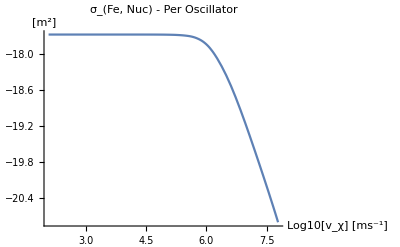

```mathematica
Plot[FeσDictNucme[["σf"]][vχ],{vχ,FeσDictNucme[["vχ"]][[1]],FeσDictNucme["vχ"][[2]]},PlotLabels->i,PlotLabel->"σ_(Fe, Nuc) - Per Oscillator",AxesLabel->{"Log10[v_χ] [ms^-1]","[m^2]"},PlotRange->{-17,-25}]
```

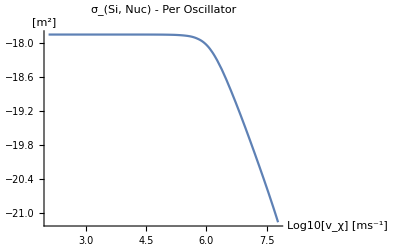

```mathematica
Plot[SiσDictNucme[["σf"]][vχ],{vχ,SiσDictNucme[["vχ"]][[1]],SiσDictNucme["vχ"][[2]]},PlotLabel->"σ_(Si, Nuc) - Per Oscillator",AxesLabel->{"Log10[v_χ] [ms^-1]","[m^2]"},PlotRange->{-17,-25}]
```

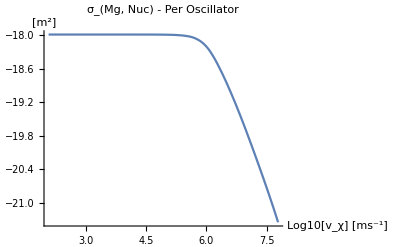

```mathematica
Plot[MgσDictNucme[["σf"]][vχ],{vχ,MgσDictNucme[["vχ"]][[1]],MgσDictNucme["vχ"][[2]]},PlotLabel->"σ_(Mg, Nuc) - Per Oscillator",AxesLabel->{"Log10[v_χ] [ms^-1]","[m^2]"},PlotRange->{-17,-25}]
```

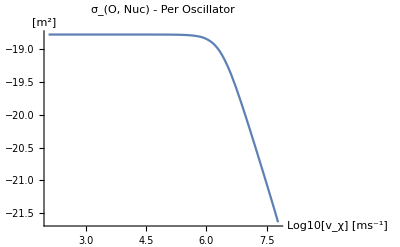

```mathematica
Plot[OσDictNucme[["σf"]][vχ],{vχ,OσDictNucme[["vχ"]][[1]],OσDictNucme["vχ"][[2]]},PlotLabel->"σ_(O, Nuc) - Per Oscillator",AxesLabel->{"Log10[v_χ] [ms^-1]","[m^2]"},PlotRange->{-17,-25}]
```

## dσ/(dE_R dΩ)

```mathematica
dσdERdΩe[ω_,cosθ_,mχ_,vχ_,κ_]:=1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))Im[-1/(Dielectrics`ϵMωq[ω,q,"νi","qF","vF"])]/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))
```

```mathematica
dσdERdΩNucFiniteT[ω_,cosθ_,mχ_,vχ_,κ_]:=1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))Im[-1/(Dielectrics`ϵMωq[ω,q,"νi","qF","vF"])]/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))
```

```mathematica
dσdERdΩe[]
```

```mathematica
(ℏ q^2)/(2 mN)/.q->(mχ vχ)/ℏ(cosθ + √(cosθ^2 - (2 ℏ ω)/(mχ vχ^2)))
Solve[%==ω,ω]
Solve[%%==ω,cosθ]
Print["largest amount of energy is transfered by small angle scattering. Large angle scattering implies small energy transfer"]
```

(mχ^2 vχ^2 (cosθ+√(cosθ^2-(2 ω ℏ)/(mχ vχ^2)))^2)/(2 mN ℏ)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ω→0},{ω→(2 cosθ^2 mN mχ^2 vχ^2)/((mN+mχ)^2 ℏ)}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{cosθ→-((mN+mχ) √ω √ℏ)/(√2 √mN mχ vχ)},{cosθ→((mN+mχ) √ω √ℏ)/(√2 √mN mχ vχ)}}

largest amount of energy is transfered by small angle scattering. Large angle scattering implies small energy transfer